v2 Updated April 30, 2020
- fixed form-factors for 3d (Xe_v2.mx)
- defined PneXenon
- fixed plot labels of dsdlogERinterp to indicate that logER is in units of Rydberg energies

```mathematica
Quit[]
```

```mathematica
<<"MyUnits.m";
```

## plot styling

```mathematica
default1=RGBColor[0.368417,0.506779,0.709798]
```

RGBColor[0.368417, 0.506779, 0.709798]

```mathematica
default2=RGBColor[0.880722,0.611041,0.142051]
```

RGBColor[0.880722, 0.611041, 0.142051]

```mathematica
default3=RGBColor[0.560181,0.691569,0.194885]
```

RGBColor[0.560181, 0.691569, 0.194885]

```mathematica
default4=RGBColor[0.922526,0.385626,0.209179]
```

RGBColor[0.922526, 0.385626, 0.209179]

```mathematica
default5=RGBColor[0.528488,0.470624,0.701351]
```

RGBColor[0.528488, 0.470624, 0.701351]

```mathematica
DefaultPlotOptions =
  {ImageSize -> 350, AspectRatio->1.0, Frame -> True, Axes -> False, PlotRangePadding -> 0,
   TicksStyle -> Black, FrameTicksStyle -> Black, LabelStyle -> { FontSize -> 16, FontFamily -> "Times",Black},
   FrameStyle -> Directive[Thickness[0.002]]};

SetOptions[Plot, DefaultPlotOptions];
SetOptions[LogPlot, DefaultPlotOptions];
SetOptions[LogLogPlot, DefaultPlotOptions];
SetOptions[LogLinearPlot, DefaultPlotOptions];
SetOptions[ListPlot, DefaultPlotOptions, Joined -> True];
SetOptions[ListLogPlot, DefaultPlotOptions, Joined -> True];
SetOptions[ListLogLinearPlot, DefaultPlotOptions, Joined -> True];
SetOptions[ListLogLogPlot, DefaultPlotOptions, Joined -> True];
SetOptions[ListContourPlot,DefaultPlotOptions];
```

```mathematica
Clear[PrettyExp]
PrettyExp[x_,MAX_: 2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]]
Clear[fticksR]
fticksR[min_,max_,AMAX_: 1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.005,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.015,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
Clear[fticksRNoLabels]
fticksRNoLabels[min_,max_,AMAX_: 1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.005,0}},{i,2,9}],{1}],{10.^x,"",{.015,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
```

## DM velocity distribution

### Load Default parameters

Standard DM local density:

```mathematica
ρDM=0.4 "GeV" ("cm")^-3;
```

Conversion to natural units:

```mathematica
kps=10^3/(3 10^8); (* km/s *)
```

Default velocity distribution parameters:

```mathematica
(*from astro-ph/9710077v1 *)
{v0,vemax,vemin}={220kps,241.279kps,212.448kps};
veave=1/2(vemax+vemin);

(*astro-ph/0611671*)
vesc=544kps;
```

### Cut off Maxwell-Boltzmann distribution (see also Savage et. al. 0808.3607)

```mathematica
(*Integrate[4π v^2(π v0^2)^(-3/2)ⅇ^(-v^2/v0^2),{v,0,vesc},Assumptions->{vesc>v0>0}]*)
Nesc[v0_,vesc_]:=Erf[vesc/v0]-(2 vesc ⅇ^(-vesc^2/v0^2))/(√π v0)
```

```mathematica
(*Integrate[ⅇ^((-(v-ve)^2)/v0^2),{v,vmin,vesc+ve}]
Integrate[ⅇ^((-(v+ve)^2)/v0^2),{v,vmin,vesc-ve}]
Integrate[ⅇ^(-vesc^2/v0^2),{v,vesc-ve,vesc+ve}]
Simplify[1/(Nesc √π v0 ve)(%%%-%%-%)]*)
ηMB1[vmin_,v0_,ve_,vesc_]:=1/(2 Nesc[v0,vesc]ve)(Erf[(ve-vmin)/v0]+Erf[(ve+vmin)/v0]-(4 ve)/(√π v0)ⅇ^(-vesc^2/v0^2))
```

```mathematica
(*Integrate[ⅇ^((-(v-ve)^2)/v0^2),{v,vmin,vesc+ve}]
Integrate[ⅇ^(-vesc^2/v0^2),{v,vmin,vesc+ve}]
Simplify[1/(Nesc √π v0 ve)(%%-%)]*)
ηMB2[vmin_,v0_,ve_,vesc_]:=1/(2 Nesc[v0,vesc]ve)(Erf[(ve-vmin)/v0]+Erf[vesc/v0]-(2(ve+vesc-vmin))/(√π v0)ⅇ^(-vesc^2/v0^2))
```

```mathematica
(*Using continous approximation to HeavisideTheta for smoother NIntegrate*)
HeavisideTheta2[x_]:=1/2(Tanh[100000x]+1)
ηMB[vesc_,v0_,ve_][vmin_]:=ηMB1[vmin,v0,ve,vesc] HeavisideTheta2[vesc-ve-vmin]+ηMB2[vmin,v0,ve,vesc] HeavisideTheta2[vesc+ve-vmin]HeavisideTheta2[vmin+ve-vesc]/."kps"->kps
ΔηMB[vesc_,v0_,vemax_,vemin_][vmin_]:=1/2(ηMB[vesc,v0,vemax][vmin]-ηMB[vesc,v0,vemin][vmin])
```

## Ionization Form-factors

### Using full outgoing electron wavefunctions

#### Load values

```mathematica
<<"Xe_v2.mx";
fsqtable["Xe5pFullAlt"]=Xe5pFullAlt;
fsqtable["Xe4dFullAlt"]=Xe4dFullAlt;
fsqtable["Xe5sFullAlt"]=Xe5sFullAlt;

fsqtable["Xe3dFullAlt"]=Xe3dFullAlt;
fsqtable["Xe4pFullAlt"]=Xe4pFullAlt;
fsqtable["Xe4sFullAlt"]=Xe4sFullAlt;

fsqtable["Xe3pFullAlt"]=Xe3pFullAlt;
```

#### plot

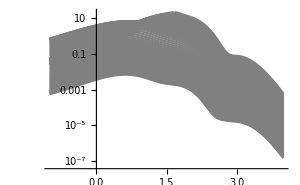
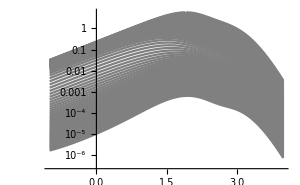
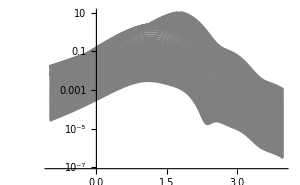
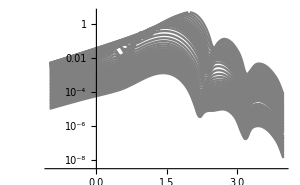
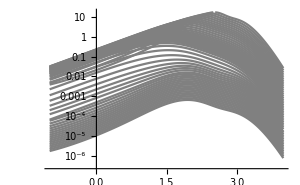
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListLogPlot[#[[2]],DataRange->#[[1,2]],PlotStyle->Gray,Joined->True,InterpolationOrder->2,ImageSize->300]&[fsqtable["Xe5pFullAlt"]],
ListLogPlot[#[[2]],DataRange->#[[1,2]],PlotStyle->Gray,Joined->True,InterpolationOrder->2,ImageSize->300]&[fsqtable["Xe4dFullAlt"]],
ListLogPlot[#[[2]],DataRange->#[[1,2]],PlotStyle->Gray,Joined->True,InterpolationOrder->2,ImageSize->300]&[fsqtable["Xe3dFullAlt"]],ListLogPlot[#[[2]],DataRange->#[[1,2]],PlotStyle->Gray,Joined->True,InterpolationOrder->2,ImageSize->300]&[fsqtable["Xe4pFullAlt"]],ListLogPlot[#[[2]],DataRange->#[[1,2]],PlotStyle->Gray,Joined->True,InterpolationOrder->2,ImageSize->300]&[fsqtable["Xe4sFullAlt"]],
ListLogPlot[#[[2]],DataRange->#[[1,2]],PlotStyle->Gray,Joined->True,InterpolationOrder->2,ImageSize->300]&[fsqtable["Xe3pFullAlt"]]}
```

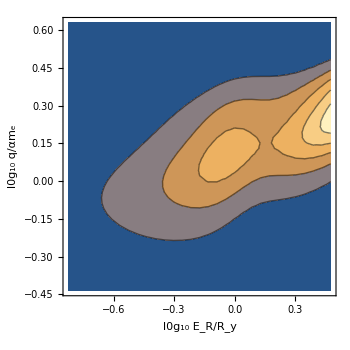
{-Graphics-,-Graphics-}

```mathematica
(*contour plot in q,Subscript[E, R] plane*)
Block[{level="Xe5pFullAlt",fsqvalues1,fsqvalues2,lnqvalues,lnkvalues},
lnqvalues=Block[{lnqmin=fsqtable["Xe5pFullAlt"][[1,2,1]],lnqmax=fsqtable["Xe5pFullAlt"][[1,2,2]],δlnq,Nq=Dimensions[fsqtable["Xe5pFullAlt"][[2]]][[2]]},
δlnq=(lnqmax-lnqmin)/(Nq-1);
Table[lnqmin+n δlnq,{n,0,Nq-1}]];lnkvalues=Block[{lnkmin=fsqtable["Xe5pFullAlt"][[1,1,1]],lnkmax=fsqtable["Xe5pFullAlt"][[1,1,2]],δlnk,Nk=Dimensions[fsqtable["Xe5pFullAlt"][[2]]][[1]]},
δlnk=(lnkmax-lnkmin)/(Nk-1);
Table[lnkmin+n δlnk,{n,0,Nk-1}]];
fsqvalues1=Flatten[Table[{(*ER*)(2lnkvalues[[j]])/Log[10],(*q*)lnqvalues[[i]]/Log[10],fsqtable["Xe5pFullAlt"][[2,j,i]]},{i,1,50(*Length[lnqvalues]*)},{j,30,60(*Length[lnkvalues]*)}],1];
fsqvalues2=Flatten[Table[{(*ER*)(2lnkvalues[[j]])/Log[10],(*q/E*)(Log[(alpha me)/(1/2 alpha^2 me)]-lnqvalues[[i]]-(2lnkvalues[[j]]))/Log[10],fsqtable["Xe5pFullAlt"][[2,j,i]]},{i,1,60(*Length[lnqvalues]*)},{j,30,60(*Length[lnkvalues]*)}],1];
{ListContourPlot[fsqvalues1,PlotRange->(*{{0,10},{0,50},All}*)All,FrameLabel->{"l0g_10 E_R/R_y","l0g_10 q/αm_e"}],ListContourPlot[fsqvalues2,PlotRange->(*{{0,10},{0,50},All}*)All,FrameLabel->{"log_10E_R/R_y","log_10q/E_R"}]}]
```

k'/αm_e = 1.

E_R = 13.6 eV

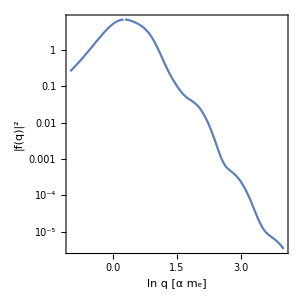

```mathematica
Block[{level="Xe5pFullAlt",Nk=49,lnkmin=-2.4,δlnk=0.05},
Print["k'/αm_e = ",ⅇ^(lnkmin+(Nk-1)δlnk)];
Print["E_R = ",ⅇ^(2(lnkmin+(Nk-1)δlnk))13.6, " eV"];ListLogPlot[#[[2,Nk]],DataRange->#[[1,2]],PlotRange->{All,All},PlotStyle->Automatic,Joined->True,InterpolationOrder->2,ImageSize->300,AxesLabel->{"ln q [α m_e]","|f(q)|^2"},Background->White]&[fsqtable[level]]]
```

ReplaceAll::reps: {toGeV} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

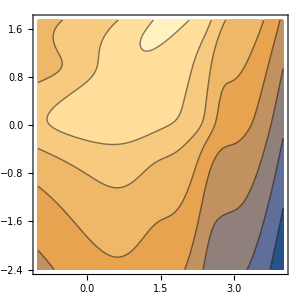

```mathematica
With[{EB=75.6"eV",mχ=100"MeV"},Show[ListContourPlot[Log10[#[[2]]],DataRange->{#[[1,2]],#[[1,1]]},ImageSize->300]&[fsqtable["Xe4dFullAlt"]],
ContourPlot[Log10[ⅇ^lnq ηMB[vesc,v0,vemax][EB/(ⅇ^lnq alpha me)+(ⅇ^(2lnK)alpha)/(2 ⅇ^lnq)+(ⅇ^lnq alpha me)/(2mχ)/.toGeV]],{lnq,-1,4},{lnK,-2.4,1.75},ImageSize->300,Contours->{1,3},ContourShading->None,ContourStyle->{{Black,Thick}}]]]
```

```mathematica
With[{EB=12.4"eV",mχ=100"MeV",level="Xe5pFullAlt"},Show[ListContourPlot[Log10[#[[2]]],DataRange->{#[[1,2]],#[[1,1]]},ImageSize->300]&[fsqtable[level]],
ContourPlot[Log10[ⅇ^lnq ηMB[vesc,v0,veave][EB/(ⅇ^lnq alpha me)+(ⅇ^(2lnK)alpha)/(2 ⅇ^lnq)+(ⅇ^lnq alpha me)/(2mχ)/.toGeV]],{lnq,-1,4},{lnK,-2.4,1.75},ImageSize->300,Contours->{1,3},ContourShading->None,ContourStyle->{{Black,Thick}}]]]
```

ReplaceAll::reps: {toGeV} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
With[{EB=25.6"eV",mχ=100"MeV",level="Xe5sFullAlt"},Show[ListContourPlot[Log10[#[[2]]],DataRange->{#[[1,2]],#[[1,1]]},ImageSize->300]&[fsqtable[level]],
ContourPlot[Log10[ⅇ^lnq ηMB[vesc,v0,veave][EB/(ⅇ^lnq alpha me)+(ⅇ^(2lnK)alpha)/(2 ⅇ^lnq)+(ⅇ^lnq alpha me)/(2mχ)/.toGeV]],{lnq,-1,4},{lnK,-2.4,1.75},ImageSize->300,Contours->{1,3},ContourShading->None,ContourStyle->{{Black,Thick}}]]]
```

ReplaceAll::reps: {toGeV} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

## Calculate Differential Ionization Rate

```mathematica
(*normalization: rate = 6.2/A events/(kg-day)×Subscript[σ̄, e]/(10^-40 cm^2)×(10MeV)/mχ×suppression*)
RateNorm=1/mproton(0.4"GeV"("cm")^-3)/(10"MeV")(10^-40("cm")^2)10^-3//Units[("kg")^-1("year")^-1]
NormXe10=With[{exposure=15"kg""day",A=131.3},exposure 1/(A  mproton)(0.4"GeV"("cm")^-3)/(1"MeV")(1("cm")^2)10^-3/.toGeV]
```

2262.49/(kg year)

7.07658×10^40

### Calculate differential cross-section values

Calculates the differential cross-section values for a given ηMB(v_esc,v_0,v_avg) and F_DM(q). **WARNING** takes order of hours to run all of the levels.

```mathematica
(*Subscript[E, B] for 5p, 5s, 4d*)
{12.4"eV",25.7"eV",75.6"eV"};
(*Subscript[E, B] for 4p, 4s, 3d*)
{163.5"eV",213.8"eV",710.7"eV"};
```

```mathematica
(*mχ values used for Xe 5p, 5s, 4d*)
{4,5,6,8,10,12,15,20,30,50,100,200,300,500,1000,3000};
{7,8,9,10,12,15,20,30,50,100,200,300,500,1000,3000};
{20,21,22,24,26,30,40,50,70,100,200,300,500,1000,3000};

(*mχ values used for Xe 4p, 4s, 3d*)
{70,100,200,300,500,1000,3000};
{70,100,200,300,500,1000,3000};
{70,100,200,300,500,1000,3000};
```

### Function giving diff cross-section from form factor

```mathematica
(*make interpolating function for each lnK: logfsqInterp[energy level][lnK][lnq]*)
logfsqInterp[level_][lnK_]:=
Module[{fsqdata,lnKmin,lnKmax,i,fsqlist,lnqrange},
fsqdata=fsqtable[level];
{lnKmin,lnKmax}={fsqdata[[1,1,1]],fsqdata[[1,1,2]]};
i=Round[1+(lnK-lnKmin)/(lnKmax-lnKmin)(Length[fsqdata[[2]]]-1)];
If[i>Length[fsqdata[[2]]]∨i<1,Print["doesn't exist"];Abort[]];
fsqlist=fsqdata[[2,i]];
lnqrange=fsqdata[[1,2]];
ListInterpolation[Log10[fsqlist],lnqrange,InterpolationOrder->2]];
```

```mathematica
(*specify a level with a previously calculated fsqtable[level]*)
(*gives table of form {{log Subscript[E, R]/Subscript[R, y],1/(10^-3 Subscript[σ̄, e])d/(d Subscript[logE, R])⟨σv⟩},...} for each mχ*)
diffxsec[level_,EB_,η_,FDM_][mχvalues_]:=
Module[{lnKmin,lnKmax,δlnK,lnqmax},
{lnKmin,lnKmax}=fsqtable[level][[1,1]];
δlnK=(lnKmax-lnKmin)/(Length[fsqtable[level][[2]]]-1);
lnqmax=fsqtable[level][[1,2,2]];
Table[Module[{lnKmax2,values},
lnKmax2=1/2 Log[(0.5mχ "MeV"(vesc+veave)^2-EB)/(0.5 alpha^2 me)/.toGeV];
values=Table[Module[{vmin,qfsq,q,qmin,qmax},
vmin=Abs[EB/(q alpha me)+(ⅇ^(2lnK)alpha)/(2q)+(q alpha me)/(2mχ"MeV")/.toGeV];(*NB Abs[...] allows EB to be set negative to include downscattering*)
qfsq=q 10^logfsqInterp[level][lnK][Log[q]];
qmin=1/(veave+vesc)(EB/(alpha me)+(ⅇ^(2lnK)alpha)/2)/.toGeV;
qmax=(2mχ"MeV")/(alpha me)(veave+vesc)/.toGeV;
{(2lnK)/Log[10.],Log[10]NIntegrate[alpha^2/(8 10^-3)qfsq η[vmin] FDM[q]^2,{q,qmin,(*Min[qmax,ⅇ^lnqmax]*)ⅇ^lnqmax},Method->"AdaptiveQuasiMonteCarlo",PrecisionGoal->3]//Quiet}],{lnK,lnKmin,Min[lnKmax,lnKmax2],δlnK}];
{mχ"MeV",Select[Chop[values,10^-14],#[[2]]>0&]}],
{mχ,mχvalues}]]
```

```mathematica
(*make interpolation function of ds/Subscript[dlogE, R] as function of log Subscript[E, R], in units of Rydberg*)
Clear[dsdlogERinterp]
dsdlogERinterp[level_,type_,mχ_]:=Module[{values},
values=Check[Select[dsdlogERdata[level,type],(#[[1]]/(mχ)/.toGeV)==1&][[1,2]],{{-1,-1},{0,-1}}];
ListInterpolation[values[[All,2]],{values[[All,1]]},InterpolationOrder->(*3*)1]]
```

#### FDM=1, type=”standard”

```mathematica
(*standard (no DM form-factor)*)
```

```mathematica
With[{level="Xe5pFullAlt",EB=12.4"eV",η=ηMB[vesc,v0,veave],type="standard",FDM=1&,
mχvalues={4,5,6,7,8,9,10,12,13,14,15,16,17,18,20,25,30,40,50,60,80,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe5pFullAlt","standard"]=%;
```

```mathematica
With[{level="Xe5sFullAlt",EB=25.7"eV",η=ηMB[vesc,v0,veave],type="standard",FDM=1&,
mχvalues={7,8,9,10,12,15,20,30,50,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe5sFullAlt","standard"]=%;
```

```mathematica
With[{level="Xe4dFullAlt",EB=75.6"eV",η=ηMB[vesc,v0,veave],type="standard",FDM=1&,
mχvalues={20,21,22,24,26,30,40,50,70,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe4dFullAlt","standard"]=%;
```

```mathematica
With[{level="Xe4sFullAlt",EB=213.8"eV",η=ηMB[vesc,v0,veave],type="standard",FDM=1&,
mχvalues={70,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe4sFullAlt","standard"]=%;
```

```mathematica
With[{level="Xe4pFullAlt",EB=163.5"eV",η=ηMB[vesc,v0,veave],type="standard",FDM=1&,
mχvalues={70,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe4pFullAlt","standard"]=%;
```

```mathematica
With[{level="Xe3dFullAlt",EB=710.7"eV",η=ηMB[vesc,v0,veave],type="standard",FDM=1&,
mχvalues={70,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe3dFullAlt","standard"]=%;
```

#### FDM~1/q, type=”EDM”

```mathematica
(*EDM (1/q DM form-factor)*)
```

```mathematica
With[{level="Xe5pFullAlt",EB=12.4"eV",η=ηMB[vesc,v0,veave],type="EDM",FDM=1/#&,
mχvalues={4,5,6,7,8,9,10,12,12.5,13,14,15,16,17,18,20,25,30,40,50,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe5pFullAlt","EDM"]=%;
```

```mathematica
With[{level="Xe5sFullAlt",EB=25.7"eV",η=ηMB[vesc,v0,veave],type="EDM",FDM=1/#&,
mχvalues={7,8,9,10,12,15,20,30,50,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe5sFullAlt","EDM"]=%;
```

```mathematica
With[{level="Xe4dFullAlt",EB=75.6"eV",η=ηMB[vesc,v0,veave],type="EDM",FDM=1/#&,
mχvalues={20,21,22,24,26,30,40,50,70,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe4dFullAlt","EDM"]=%;
```

```mathematica
With[{level="Xe4sFullAlt",EB=213.78"eV",η=ηMB[vesc,v0,veave],type="EDM",FDM=1/#&,
mχvalues={70,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe4sFullAlt","EDM"]=%;
```

```mathematica
With[{level="Xe4pFullAlt",EB=163.49"eV",η=ηMB[vesc,v0,veave],type="EDM",FDM=1/#&,
mχvalues={70,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe4pFullAlt","EDM"]=%;
```

#### FDM~1/q^2, type=”LIGHT”

```mathematica
(*LIGHT (1/q^2 DM form-factor)*)
```

```mathematica
With[{level="Xe5pFullAlt",EB=12.4"eV",η=ηMB[vesc,v0,veave],type="LIGHT",FDM=1/#^2&,
mχvalues={4,5,6,7,8,9,10,12,13,14,15,17,20,25,30,40,50,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe5pFullAlt","LIGHT"]=%;
```

```mathematica
With[{level="Xe5sFullAlt",EB=25.7"eV",η=ηMB[vesc,v0,veave],type="LIGHT",FDM=1/#^2&,
mχvalues={7,8,9,10,12,15,20,30,50,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe5sFullAlt","LIGHT"]=%;
```

```mathematica
With[{level="Xe4dFullAlt",EB=75.6"eV",η=ηMB[vesc,v0,veave],type="LIGHT",FDM=1/#^2&,
mχvalues={20,21,22,24,26,30,40,50,70,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe4dFullAlt","LIGHT"]=%;
```

```mathematica
With[{level="Xe4sFullAlt",EB=213.78"eV",η=ηMB[vesc,v0,veave],type="LIGHT",FDM=1/#^2&,
mχvalues={70,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe4sFullAlt","LIGHT"]=%;
```

```mathematica
With[{level="Xe4pFullAlt",EB=163.49"eV",η=ηMB[vesc,v0,veave],type="LIGHT",FDM=1/#^2&,
mχvalues={70,100,200,300,500,1000,3000}},
diffxsec[level,EB,η,FDM][mχvalues]];
dsdlogERdata["Xe4pFullAlt","LIGHT"]=%;
```

## Plot Differential Rate Spectra

### define ds/dlogER

```mathematica
(*make interpolation function of ds/Subscript[dlogE, R] as function of log Subscript[E, R], in units of Rydberg*)
Clear[dsdlogERinterp];
dsdlogERinterp[level_,type_,mχ_]:=Module[{values},
values=Check[Select[dsdlogERdata[level,type],(#[[1]]/mχ/.toGeV)==1&][[1,2]],{{-1,-1},{0,-1}}];
ListInterpolation[values[[All,2]],{values[[All,1]]},InterpolationOrder->3]]
```

```mathematica
(*Plot differential suppression factors for all three levels*)
Module[{type,yrange,ticks,levels,styles,mχ},
type="standard";yrange={0.001,10};
(*type="LIGHT";yrange={10^-6,0.01};*)
(*type="EDM";yrange={10^-5,0.1};*)
mχ=10;
ticks={{Automatic,None},{(*logticks[-1,3,Log10[1/13.6]]*)Automatic,None}};
levels={"Xe5pFullAlt","Xe5pFull","Xe5p","Xe5sFullAlt","Xe5s","Xe4dFullAlt","Xe4d"};
styles={{{Darker[Blue,0.5]}},{{Darker[Blue,0.5],Dotted}},{{Darker[Blue,0.5],Dashed}},{{Darker[Red,0.5]}},{{Darker[Red,0.5],Dashed}},{{Darker[Green,0.5]}},{{Darker[Green,0.5],Dashed}}};

LogPlot[{30/mχ#1[logER],-1},{logER,#1[[1,1,1]],#1[[1,1,2]]},ImageSize->300,Frame->True,Axes->False,PlotRange->{Log10[{0.1,1000}/13.6],yrange},FrameLabel->{"log_10(E_R/13.6 eV)","(30 MeV)/m_χ1/10^-3(d ⟨σv⟩)/(d SubscriptBox[log, 10] (SubscriptBox[E, R]/13.6 eV))"},PlotStyle->styles[[1]],FrameTicks->ticks,PlotLabel->Row[{"m_χ = ",mχ," MeV"}]]
&[dsdlogERinterp[levels[[1]],type,mχ"MeV"]//Quiet]]
```

### convolve with probability function to obtain dR/dne

```mathematica
(*probability to get ne ionized electrons given recoil energy ER*)
(*assuming 1 primary electron, with a probability (1-fR) to avoid recombination, and an extra N0+Floor[ER/W] quanta, each of which has a probability (1-fR)fe0 to be an electron*)
(*N0 is the number of quanta produced by the associated de-excitation photon*)
(*W≃14 "eV"*)
(*N=-1 gives probability 1, i.e. counts all events*)
PneXenon[fR_,fe0_,W_,N0_][ne_,ER_]:=
If[ne==-1,1,
Module[{Nmax,fe},
Nmax=N0+Floor[ER/W/.toGeV];
fe=(1-fR)fe0;
fR * PDF[BinomialDistribution[Nmax,fe],ne]+(1-fR)PDF[BinomialDistribution[Nmax,fe],ne-1]]]
```

```mathematica
(*calculate cross-section / suppression factor s≡⟨σv⟩/(10^-3 Subscript[σ̄, e]) by integrating dsdlogER*)
Clear[suppression];
suppression[level_,type_,fR_,fe0_,W_,N0_:0][mχ_,ne_]:=Module[{dsdlogER},
dsdlogER=dsdlogERinterp[level,type,mχ];
(*Print[LogPlot[{dsdlogER[logER],PNelectrons[N,fR,fe0,W,N0][13.6 10^logER"eV"]dsdlogER[logER]},{logER,dsdlogER[[1,1,1]],dsdlogER[[1,1,2]]+0.1},PlotRange->All]];*)
NIntegrate[PneXenon[(*ne,*)fR,fe0,W,N0][ne,13.6 10^logER"eV"]dsdlogER[logER],{logER,dsdlogER[[1,1,1]],dsdlogER[[1,1,2]]},Method->"AdaptiveQuasiMonteCarlo",PrecisionGoal->(*2*)10,WorkingPrecision->20]//Quiet]
```

```mathematica
(*suppression factor for events producing N electrons*)
(*assuming ~13eV photon from 5s ionization gives a second electron with ER=1eV, corresponding to 1 extra quanta*)
(*and that ~63eV photon from 4d always gives 2nd electron with ER≃50 eV, corresponding to 4 extra quanta*)
suppNelectronsXe5p[type_,mχ_,N_,fR_,fe0_,W_]:=suppression["Xe5pFullAlt",type,fR,fe0,W,0][mχ,N] (* -12.4 eV *)
suppNelectronsXe5s[type_,mχ_,N_,fR_,fe0_,W_]:=suppression["Xe5sFullAlt",type,fR,fe0,W,0][mχ,N] (* -25.7 eV *)
suppNelectronsXe4d[type_,mχ_,N_,fR_,fe0_,W_]:=suppression["Xe4dFullAlt",type,fR,fe0,W,4][mχ,N] (* -75.59 eV *)
(*and that ~150 eV photon from 4p always gives 2nd electron with ER≃139 eV, corresponding to 6-10 extra quanta*)
(*and that ~230 eV photon from 4s always gives 2nd electron with ER≃218 eV, corresponding to 3-15 extra quanta*)
suppNelectronsXe4p[type_,mχ_,N_,fR_,fe0_,W_,ne_]:=suppression["Xe4pFullAlt",type,fR,fe0,W,ne][mχ,N](* -163.49 eV *)
suppNelectronsXe4s[type_,mχ_,N_,fR_,fe0_,W_,ne_]:=suppression["Xe4sFullAlt",type,fR,fe0,W,ne][mχ,N](* -213.78 eV *)
```

```mathematica
(*normalization: rate = 6.2/A events/(kg-day)×Subscript[σ̄, e]/(10^-40 cm^2)×(10MeV)/mχ×suppression*)
RateNorm=1/mproton(0.4"GeV"("cm")^-3)/(10"MeV")(10^-40("cm")^2)10^-3//Units[("kg")^-1("year")^-1]
With[{A=131.},RateNormXe[mχ_,σe_]:=6.2/A 1/("kg""day")σe/(10^-40("cm")^2)(10 "MeV")/mχ(365.25 "day")/("year")]
```

2262.49/(kg year)

#### Create NumEventsFiduc tables

```mathematica
mχList={1000"MeV",500"MeV",100"MeV"};
```

```mathematica
(* FDM=1 "standard" *)
Table[With[{mχ=mχList[[jj]],fR=0.0,fe0=0.8,Nmax=20,W=14"eV",exposure=1 "kg" "year",σe=1("cm")^2},
levels={"Xe5pFullAlt","Xe5sFullAlt","Xe4dFullAlt","Xe4sFullAlt","Xe4pFullAlt"};
NumEventsFiduc[mχ,"Xe5pFullAlt","standard"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe5p["standard",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"Xe5sFullAlt","standard"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe5s["standard",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"Xe4dFullAlt","standard"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe4d["standard",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];NumEventsFiduc[mχ,"Xe4sFullAlt","standard"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe] suppNelectronsXe4s["standard",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];NumEventsFiduc[mχ,"Xe4pFullAlt","standard"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe4p["standard",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"tot","standard"]=Table[{Ne-0.5,Sum[NumEventsFiduc[mχ,levels[[ii]],"standard"][[Ne,2]],{ii,1,Length[levels]}]},{Ne,1,Nmax}];],{jj,1,Length[mχList]}];
```

```mathematica
(* FDM=1 "mod" *)
Table[With[{mχ=mχList[[jj]],fR=0.0,fe0=0.8,Nmax=20,W=14"eV",exposure=1 "kg" "year",σe=1("cm")^2},
levels={"Xe5pFullAlt","Xe5sFullAlt","Xe4dFullAlt","Xe4sFullAlt","Xe4pFullAlt"};
NumEventsFiduc[mχ,"Xe5pFullAlt","mod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe5p["mod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"Xe5sFullAlt","mod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe5s["mod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"Xe4dFullAlt","mod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe4d["mod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];NumEventsFiduc[mχ,"Xe4sFullAlt","mod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe] suppNelectronsXe4s["mod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];NumEventsFiduc[mχ,"Xe4pFullAlt","mod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe4p["mod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"tot","mod"]=Table[{Ne-0.5,Sum[NumEventsFiduc[mχ,levels[[ii]],"mod"][[Ne,2]],{ii,1,Length[levels]}]},{Ne,1,Nmax}];],{jj,1,Length[mχList]}];
```

```mathematica
(* FDM=1 "DailyMod" *)
Table[With[{mχ=mχList[[jj]],fR=0.0,fe0=0.8,Nmax=20,W=14"eV",exposure=1 "kg" "year",σe=1("cm")^2},
levels={"Xe5pFullAlt","Xe5sFullAlt","Xe4dFullAlt","Xe4sFullAlt","Xe4pFullAlt"};
NumEventsFiduc[mχ,"Xe5pFullAlt","DailyMod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe5p["DailyMod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"Xe5sFullAlt","DailyMod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe5s["DailyMod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"Xe4dFullAlt","DailyMod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe4d["DailyMod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];NumEventsFiduc[mχ,"Xe4sFullAlt","DailyMod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe] suppNelectronsXe4s["DailyMod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];NumEventsFiduc[mχ,"Xe4pFullAlt","DailyMod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe4p["DailyMod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"tot","DailyMod"]=Table[{Ne-0.5,Sum[NumEventsFiduc[mχ,levels[[ii]],"DailyMod"][[Ne,2]],{ii,1,Length[levels]}]},{Ne,1,Nmax}];],{jj,1,Length[mχList]}]
```

{Null,Null,Null}

```mathematica
(* FDM~1/q^2"LIGHT" *)
Table[With[{mχ=mχList[[jj]],fR=0.0,fe0=0.8,Nmax=20,W=14"eV",exposure=1 "kg" "year",σe=1("cm")^2},
levels={"Xe5pFullAlt","Xe5sFullAlt","Xe4dFullAlt","Xe4sFullAlt","Xe4pFullAlt"};
NumEventsFiduc[mχ,"Xe5pFullAlt","LIGHT"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe5p["LIGHT",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"Xe5sFullAlt","LIGHT"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe5s["LIGHT",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"Xe4dFullAlt","LIGHT"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe4d["LIGHT",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];NumEventsFiduc[mχ,"Xe4sFullAlt","LIGHT"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe] suppNelectronsXe4s["LIGHT",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];NumEventsFiduc[mχ,"Xe4pFullAlt","LIGHT"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe4p["LIGHT",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"tot","LIGHT"]=Table[{Ne-0.5,Sum[NumEventsFiduc[mχ,levels[[ii]],"LIGHT"][[Ne,2]],{ii,1,Length[levels]}]},{Ne,1,Nmax}];],{jj,1,Length[mχList]}]
```

{Null,Null,Null}

```mathematica
(* FDM~1/q^2"LIGHTmod" *)
Table[With[{mχ=mχList[[jj]],fR=0.0,fe0=0.8,Nmax=20,W=14"eV",exposure=1 "kg" "year",σe=1("cm")^2},
levels={"Xe5pFullAlt","Xe5sFullAlt","Xe4dFullAlt","Xe4sFullAlt","Xe4pFullAlt"};
NumEventsFiduc[mχ,"Xe5pFullAlt","LIGHTmod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe5p["LIGHTmod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"Xe5sFullAlt","LIGHTmod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe5s["LIGHTmod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"Xe4dFullAlt","LIGHTmod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe4d["LIGHTmod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];NumEventsFiduc[mχ,"Xe4sFullAlt","LIGHTmod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe] suppNelectronsXe4s["LIGHTmod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];NumEventsFiduc[mχ,"Xe4pFullAlt","LIGHTmod"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe4p["LIGHTmod",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"tot","LIGHTmod"]=Table[{Ne-0.5,Sum[NumEventsFiduc[mχ,levels[[ii]],"LIGHTmod"][[Ne,2]],{ii,1,Length[levels]}]},{Ne,1,Nmax}];],{jj,1,Length[mχList]}]
```

{Null,Null,Null}

```mathematica
(* FDM~1/q^2"DailyModLIGHT" *)
Table[With[{mχ=mχList[[jj]],fR=0.0,fe0=0.8,Nmax=20,W=14"eV",exposure=1 "kg" "year",σe=1("cm")^2},
levels={"Xe5pFullAlt","Xe5sFullAlt","Xe4dFullAlt","Xe4sFullAlt","Xe4pFullAlt"};
NumEventsFiduc[mχ,"Xe5pFullAlt","DailyModLIGHT"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe5p["DailyModLIGHT",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"Xe5sFullAlt","DailyModLIGHT"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe5s["DailyModLIGHT",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"Xe4dFullAlt","DailyModLIGHT"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe4d["DailyModLIGHT",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];NumEventsFiduc[mχ,"Xe4sFullAlt","DailyModLIGHT"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe] suppNelectronsXe4s["DailyModLIGHT",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];NumEventsFiduc[mχ,"Xe4pFullAlt","DailyModLIGHT"]=Table[{Ne-0.5,exposure RateNormXe[mχ,σe]suppNelectronsXe4p["DailyModLIGHT",mχ,Ne,fR,fe0,W]},{Ne,1,Nmax}];
NumEventsFiduc[mχ,"tot","DailyModLIGHT"]=Table[{Ne-0.5,Sum[NumEventsFiduc[mχ,levels[[ii]],"DailyModLIGHT"][[Ne,2]],{ii,1,Length[levels]}]},{Ne,1,Nmax}];],{jj,1,Length[mχList]}]
```

{Null,Null,Null}

```mathematica
(* varying secondary ionization parameters "standard"*)
Wlist={12.4 "eV",13.0 "eV",14.5 "eV",16.0 "eV"};
ne1list={6,10};
ne2list={3,15};
Table[Module[{mχ,Nmax,exposure,σe,fR,fe0,W,type,NumEventsRange},
mχ=mχList[[ll]];Nmax=20;exposure=1 "kg" "year";σe=1("cm")^2;
type="standard";
NumEvents[mχ,type]={};
For[Ne=0,Ne<Nmax,Ne++,
NumEventsRange={};
For[kk=1,kk<4,kk++,
For[ii=0,ii<3,ii++,
For[jj=1,jj≤Length[Wlist],jj++,
Table[
fR=ii*0.1; (* 0 < fR < 0.2 *)
NexNi=0.1*kk;  (* 0.1 < Nex/Ni < 0.3 *)
fe0=(1-fR)(1+NexNi)^-1;
W=Wlist[[jj]];
ne1=ne1list[[mm]];
ne2=ne2list[[mm]];
AppendTo[NumEventsRange,exposure RateNormXe[mχ,σe](suppNelectronsXe5p[type,mχ,Ne,fR,fe0,W]+suppNelectronsXe5s[type,mχ,Ne,fR,fe0,W]+suppNelectronsXe4d[type,mχ,Ne,fR,fe0,W]+suppNelectronsXe4s[type,mχ,Ne,fR,fe0,W,ne1]+suppNelectronsXe4p[type,mχ,Ne,fR,fe0,W,ne2])]
,{mm,1,Length[ne1list]}]
]
]
]
AppendTo[NumEvents[mχ,type],{Ne-0.5,Min[NumEventsRange],Max[NumEventsRange]}]
]
]
,{ll,1,Length[mχList]}]
```

{Null,Null,Null}

```mathematica
(* varying secondary ionization parameters "LIGHT"*)
Wlist={12.4 "eV",13.0 "eV",14.5 "eV",16.0 "eV"};
ne1list={6,10};
ne2list={3,15};
Table[Module[{mχ,Nmax,exposure,σe,fR,fe0,W,type,NumEventsRange},
mχ=mχList[[ll]];Nmax=20;exposure=1 "kg" "year";σe=1("cm")^2;
type="LIGHT";
NumEvents[mχ,type]={};
For[Ne=0,Ne<Nmax,Ne++,
NumEventsRange={};
For[kk=1,kk<4,kk++,
For[ii=0,ii<3,ii++,
For[jj=1,jj≤Length[Wlist],jj++,
Table[
fR=ii*0.1; (* 0 < fR < 0.2 *)
NexNi=0.1*kk;  (* 0.1 < Nex/Ni < 0.3 *)
fe0=(1-fR)(1+NexNi)^-1;
W=Wlist[[jj]];
ne1=ne1list[[mm]];
ne2=ne2list[[mm]];
AppendTo[NumEventsRange,exposure RateNormXe[mχ,σe](suppNelectronsXe5p[type,mχ,Ne,fR,fe0,W]+suppNelectronsXe5s[type,mχ,Ne,fR,fe0,W]+suppNelectronsXe4d[type,mχ,Ne,fR,fe0,W]+suppNelectronsXe4s[type,mχ,Ne,fR,fe0,W,ne1]+suppNelectronsXe4p[type,mχ,Ne,fR,fe0,W,ne2])]
,{mm,1,Length[ne1list]}]
]
]
]
AppendTo[NumEvents[mχ,type],{Ne-0.5,Min[NumEventsRange],Max[NumEventsRange]}]
]
]
,{ll,1,Length[mχList]}]
```

$Aborted

#### 1 GeV, standard

```mathematica
Clear[fticksR1GeVStandard]
fticksR1GeVStandard[min_,max_,AMAX_: 1]:=Flatten[Table[Prepend[Flatten[Table[{10^-42/(4. 10^-44) i*10.^x,"",{.005,0}},{i,2,9}],{1}],{10^-42/(4. 10^-44)10.^x,PrettyExp[x,AMAX],{.015,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
```

```mathematica
(*plot histogram*)
With[{mχ=1000"MeV",fR=0.0,fe0=0.8,Nmax=20,W=14"eV",exposure=500 "kg" "year",σe=4 10^-44("cm")^2},
ListLogPlot[{{#1,#2 exposure/("kg" "year") σe/("cm")^2}&@@@ NumEventsFiduc[mχ,"Xe5pFullAlt","standard"],
{#1,#2 exposure/("kg" "year") σe/("cm")^2}&@@@NumEventsFiduc[mχ,"Xe5sFullAlt","standard"],
{#1,#2 exposure/("kg" "year") σe/("cm")^2}&@@@NumEventsFiduc[mχ,"Xe4dFullAlt","standard"],{#1,#2 exposure/("kg" "year") σe/("cm")^2}&@@@NumEventsFiduc[mχ,"Xe4sFullAlt","standard"],{#1,#2 exposure/("kg" "year") σe/("cm")^2}&@@@NumEventsFiduc[mχ,"Xe4pFullAlt","standard"]},Joined->True,InterpolationOrder->0,Frame->True,FrameTicks->{{fticksR[10^-10,10^10,1],fticksR1GeVStandard[10^-10,10^10,1]},{Table[{ii,ToString[ii]},{ii,0,30}],Automatic}},FrameTicksStyle->{{Black,Black},{13,Black}},FrameLabel->{"Ne","Current constraints ((σ̄)_e = 4x10^-44 cm^2)","Number of Events","Freeze-out ((σ̄)_e = 10^-42 cm^2)"},Axes->False,(*PlotRange->{{0,16},{10^-7,1}},*)PlotRangePadding->{{0,0},{0,0.2}}]]
ShellEvents[1000"MeV","standard"]=%;
```

-Graphics-

```mathematica
(*plot histogram*)
With[{mχ=1000"MeV",fR=0.0,fe0=0.8,Nmax=20,W=14"eV",exposure=500 "kg" "year",σe=4 10^-44("cm")^2},

ListLogPlot[{#1,#2 exposure/("kg" "year") σe/("cm")^2}&@@@NumEventsFiduc[mχ,"tot","standard"],Joined->True,InterpolationOrder->0,Frame->True,FrameLabel->{"Ne","Maximum number of events\n(30 kg-year, (σ̄)_e = 4x10^-44 cm^2)"},Axes->False,PlotRange->{All,{10^-5,0.1}},PlotRangePadding->{{0,0},{0,0.2}},PlotStyle->Black]]
TotNevents[1000"MeV","standard"]=%;
```

-Graphics-

```mathematica
(*NumEvents[1000"MeV","standard"]=tmpNumEvents*)
```

{{-0.5,0.,0.00246971},{0.5,0.00682401,0.0111387},{1.5,0.00473362,0.00650488},{2.5,0.00174464,0.00535979},{3.5,0.00225762,0.0049322},{4.5,0.00296809,0.00534867},{5.5,0.00162312,0.00387969},{6.5,0.000851238,0.00262569},{7.5,0.000428512,0.00205503},{8.5,0.000211237,0.00174254},{9.5,0.00010349,0.00120768},{10.5,0.000049686,0.000833211},{11.5,0.0000228875,0.000581779},{12.5,0.000010005,0.000413305},{13.5,4.1487×10^-6,0.000300774},{14.5,1.63491×10^-6,0.000218363},{15.5,6.11891×10^-7,0.000151069},{16.5,2.16618×10^-7,0.000103745},{17.5,7.19986×10^-8,0.0000707877},{18.5,2.23468×10^-8,0.0000479491}}

```mathematica
With[{mχ=1000"MeV",type="standard"},TotErrorPlot[mχ,type]=ListLogPlot[{{#1,#2 500./30}&@@@NumEvents[mχ,type],{#1,#3 500./30}&@@@NumEvents[mχ,type]},InterpolationOrder->0,PlotStyle->{{Black,Opacity[0]},{Opacity[0],Black}},Filling->{2->{1}},FillingStyle->Directive[Opacity[0.1],Black](*,PlotRange->{All,{0.1,10^6}}*)]]
```

-Graphics-

### plots of dR/dne

```mathematica
With[{mχ=1000"MeV",type="standard"},Show[ShellEvents[mχ,type],TotNevents[mχ,type],TotErrorPlot[mχ,type],PlotRange->{{0.5,18.5},{-11.5,-1}},FrameLabel->{"Ne","Current constraints ((σ̄)_e = 4x10^-44 cm^2)","Number of Events","Freeze-out ((σ̄)_e = 10^-42 cm^2)"},BaseStyle->{FontFamily->"Times",FontSize->16},(*FrameTicks->{{Table[{ii,("10")^ToString[ii]},{ii,-20,15}],Table[{Log10[10^ii 10^-42/(4 10^-44)],("10")^ToString[ii]},{ii,-20,15}]},{Table[{2 ii,ToString[ii 2]},{ii,0,20}],(*Table[{2 ii+1,ToString[ii 2+1]},{ii,0,20}]*)Automatic}},*)Epilog->{Inset[Style["F_DM=1\nm_χ=1 GeV",FontSize->16,Black],Scaled[{0.8,0.85}]],(*Inset[Style["30 kg-years",FontSize->13,Black],Scaled[{0.15,0.95}]],*)Inset[Style["5p",FontSize->16,default1],Scaled[{0.25,0.6}]],Inset[Style["5s",FontSize->16,default2],Scaled[{0.33,0.25}]],Inset[Style["4d",FontSize->16,default3],Scaled[{0.13,0.3}]],Inset[Style["4p",FontSize->16,default5],Scaled[{0.25,0.1}]],Inset[Style["3d",FontSize->16,default4],Scaled[{0.62,0.115}]]}]]
```

-Graphics-

## Find Limits

### Statistics

```mathematica
(* calculate number of events at 90% CL *)
(* Gaussian *)
nevents90CLhigh[n_]:=n+1.65 √n
nevents95CLhigh[n_]:=n+1.96 √n
nevents90CLlow[n_]:=n-1.65 √n
nevents95CLlow[n_]:=n-1.96 √n
```

two-sided bounds

```mathematica
(*(* Poisson, goes up to n=100 *)
Clear[Poisson90CL,Poisson95CL,Poisson99CL]
PoissonTable=Drop[Import["Poisson_Table.dat","table"],2];
Poisson90CL[n_]:=PoissonTable[[n+1,3]];
Poisson95CL[n_]:=PoissonTable[[n+1,5]];
Poisson99CL[n_]:=PoissonTable[[n+1,7]];

Poisson90CL[0]:=3.00;
Poisson95CL[0]:=3.69;
Poisson99CL[0]:=5.30;*)
```

one-sided bounds

```mathematica
Poisson90CLlow[n_]:=InverseGammaRegularized[1+Floor[n],1-0.1]
Poisson95CLlow[n_]:=InverseGammaRegularized[1+Floor[n],1-0.05]
Poisson99CLlow[n_]:=InverseGammaRegularized[1+Floor[n],1-0.01]
Poisson90CLhigh[n_]:=InverseGammaRegularized[1+Floor[n],0.1]
Poisson95CLhigh[n_]:=InverseGammaRegularized[1+Floor[n],0.05]
Poisson99CLhigh[n_]:=InverseGammaRegularized[1+Floor[n],0.01]
```

```mathematica
Poisson90CLlow[1]
Poisson90CLhigh[1]
```

0.531812

3.88972

### create dN/dne functions

create spectra dN/dne as a function of mχ for fiducial secondary ionization parameters

```mathematica
(*make interpolation function of ds/Subscript[dlogE, R] as function of log Subscript[E, R], in units of Rydberg*)
Clear[dsdlogERinterp];
dsdlogERinterp[level_,type_,mχ_]:=Module[{values},
values=Check[Select[dsdlogERdata[level,type],(#[[1]]/mχ/.toGeV)==1&][[1,2]],{{-1,-1},{0,-1}}];
ListInterpolation[values[[All,2]],{values[[All,1]]},InterpolationOrder->3]]
```

```mathematica
(*probability to get ne ionized electrons*)
(*assuming 1 primary electron, with a probability (1-fR) to avoid recombination, and an extra N0+Floor[ER/W] quanta, each of which has a probability (1-fR)fe0 to be an electron*)
(*N0 is the number of quanta produced by the associated de-excitation photon*)
(*W≃14 "eV"*)
(*N=-1 gives probability 1, i.e. counts all events*)
PNelectronsv2[ne_,fR_,fe0_,W_,N0_][ER_]:=
If[ne==-1,1,
Module[{Nmax,fe},
Nmax=N0+Floor[ER/W(*/.toGeV*)];
fe=(1-fR)fe0;
fR PDF[BinomialDistribution[Nmax,fe],ne]+
(1-fR)PDF[BinomialDistribution[Nmax,fe],ne-1]]]
```

```mathematica
(*calculate cross-section / suppression factor s≡⟨σv⟩/(10^-3 Subscript[σ̄, e]) by integrating dsdlogER*)
(*optional argument Nmin chooses events with at least Nmin electrons, according to the probability above*)
suppression[level_,type_,mχ_,ne_,fR_,fe0_,W_:14"eV",N0_:0]:=Module[{dsdlogER},
dsdlogER=dsdlogERinterp[level,type,mχ];
(*Print[LogPlot[{dsdlogER[logER],PNelectrons[N,fR,fe0,W,N0][13.6 10^logER"eV"]dsdlogER[logER]},{logER,dsdlogER[[1,1,1]],dsdlogER[[1,1,2]]+0.1},PlotRange->All]];
*)
NIntegrate[PNelectronsv2[ne,fR,fe0,W,N0][13.6 10^logER "eV"]dsdlogER[logER],{logER,dsdlogER[[1,1,1]],dsdlogER[[1,1,2]]},Method->"AdaptiveQuasiMonteCarlo",PrecisionGoal->(*2*)10,WorkingPrecision->20]]
```

```mathematica
(*(*suppression factor for events producing N electrons*)
(*assuming ~13eV photon from 5s ionization gives a second electron with ER=1eV, corresponding ot 1 extra quanta*)
(*and that ~63eV photon from 4d always gives 2nd electron with ER≃50 eV, corresponding to 4 extra quanta*)
suppNelectronsXe5p[type_,mχ_,N_,fR_,fe0_,W_]:=suppression["Xe5pFullAlt",type,mχ,N,fR,fe0,W,0]
suppNelectronsXe5s[type_,mχ_,N_,fR_,fe0_,W_]:=suppression["Xe5sFullAlt",type,mχ,N,fR,fe0,W,0]
suppNelectronsXe4d[type_,mχ_,N_,fR_,fe0_,W_]:=suppression["Xe4dFullAlt",type,mχ,N,fR,fe0,W,4]
suppNelectronsXe4s[type_,mχ_,N_,fR_,fe0_,W_]:=suppression["Xe4sFullAlt",type,mχ,N,fR,fe0,W,6]
suppNelectronsXe4p[type_,mχ_,N_,fR_,fe0_,W_]:=suppression["Xe4pFullAlt",type,mχ,N,fR,fe0,W,14]*)
```

```mathematica
(*make function Subscript[log, 10] suppNelectrons[logmχ], for individual levels*)
logsuppNelectrons[level_,type_,N_,fR_,fe0_,W_,N0_]:=Module[{mχ,values,goodvalues,interp},
values=Table[{{mχ/("MeV")/.toGeV},suppression[level,type,mχ,N,fR,fe0,W,N0]},{mχ,dsdlogERdata[level,type][[All,1]]}];
goodvalues=Select[values,#[[2]]>0&];
interp=ListInterpolation[Log10[goodvalues],InterpolationOrder->3(*3*)];
(*Evaluate@Piecewise[{{Quiet@interp[#],interp[[1,1,1]]-0.1<#},{-∞,#<interp[[1,1,1]]-0.1}}]&*)
Evaluate@Piecewise[{{Quiet@interp[#],interp[[1,1,1]]-0.1<#},{-∞,#<interp[[1,1,1]]-0.1}}]&]//Quiet
```

```mathematica
(*combine levels to make function Subscript[log, 10] suppNelectrons[logmχ]*)
logsuppcombined[type_,N_,fR_,fe0_,W_,N05s_,N04d_,N04s_,N04p_][logmχ_]:=Module[{logsuppXe5p,logsuppXe5s,logsuppXe4d,logsuppXe4s,logsuppXe4p},
logsuppXe5p=logsuppNelectrons["Xe5pFullAlt",type,N,fR,fe0,W,0];
logsuppXe5s=logsuppNelectrons["Xe5sFullAlt",type,N,fR,fe0,W,N05s];
logsuppXe4d=logsuppNelectrons["Xe4dFullAlt",type,N,fR,fe0,W,N04d];
logsuppXe4s=logsuppNelectrons["Xe4sFullAlt",type,N,fR,fe0,W,N04s];
logsuppXe4p=logsuppNelectrons["Xe4pFullAlt",type,N,fR,fe0,W,N04p];
Evaluate@Log10[10^logsuppXe5p[logmχ]+10^logsuppXe5s[logmχ]+10^logsuppXe4d[logmχ]+10^logsuppXe4s[logmχ]+10^logsuppXe4p[logmχ]]]
```

```mathematica
(* arrays of dN/dne for individual levels *)
dNdneFIDUClevels[type_,level_,N0_,logmχ_]:=With[{fR=0,fe=0.83,W=13.8"eV",N05s=0,N04d=4,N04s=6,N04p=16},Module[{logsupp,N,dNdneArray,dNdne,norm},
dNdneArray={};
norm=With[{exposure=1"kg""day",A=131.3,σe=10^-36("cm")^2},exposure 1/(A  mproton)(0.4"GeV"("cm")^-3)/(1"MeV")σe 10^-3/.toGeV];
For[N=1,N<15,N++,
logsupp=logsuppNelectrons[level,type,N,fR,fe,W,N0][logmχ];
dNdne=Log10[norm] +logsupp-logmχ;
AppendTo[dNdneArray,{N,dNdne}];
];
dNdneArray]]//Quiet
```

```mathematica
(* arrays of dN/dne *)
dNdneFIDUC[type_,logmχ_]:=With[{fR=0,fe=0.83,W=13.8"eV",N05s=0,N04d=4,N04s=6,N04p=14},Module[{logsupp,N,dNdneArray,dNdne,norm},
dNdneArray={};
norm=With[{exposure=1"kg""day",A=131.3,σe=10^-36("cm")^2},exposure 1/(A  mproton)(0.4"GeV"("cm")^-3)/(1"MeV")σe 10^-3/.toGeV];
For[N=1,N<15,N++,
logsupp=logsuppcombined[type,N,fR,fe,W,N05s,N04d,N04p,N04s][logmχ];
dNdne=Log10[norm] +logsupp-logmχ;
AppendTo[dNdneArray,{N,dNdne}];
];
dNdneArray]]//Quiet
```

Creating the table takes a very long time (~6 hours for each table).

```mathematica
dNdneFIDUCstandardlevels["Xe5pFullAlt"]=Table[{logm,dNdneFIDUClevels["standard","Xe5pFullAlt",0,logm]},{logm,0.75,Log10[5000],0.25}]
```

```mathematica
dNdneFIDUCstandardlevels["Xe5sFullAlt"]=Table[{logm,dNdneFIDUClevels["standard","Xe5sFullAlt",0,logm]},{logm,0.75,Log10[5000],0.25}]
```

```mathematica
dNdneFIDUCstandardlevels["Xe4dFullAlt"]=Table[{logm,dNdneFIDUClevels["standard","Xe4dFullAlt",4,logm]},{logm,0.75,Log10[5000],0.25}]
```

```mathematica
dNdneFIDUCstandardlevels["Xe4sFullAlt"]=Table[{logm,dNdneFIDUClevels["standard","Xe4sFullAlt",6,logm]},{logm,0.75,Log10[5000],0.25}]
```

```mathematica
dNdneFIDUCstandardlevels["Xe4pFullAlt"]=Table[{logm,dNdneFIDUClevels["standard","Xe4pFullAlt",14,logm]},{logm,0.75,Log10[5000],0.25}]
```

```mathematica
dNdneFIDUCstandard=Table[{logm,dNdneFIDUC["standard",logm]},{logm,0.75,Log10[5000],0.25}]
```

individual levels for light mediator

```mathematica
dNdneFIDUClightlevels["Xe5pFullAlt"]=Table[{logm,dNdneFIDUClevels["LIGHT","Xe5pFullAlt",0,logm]},{logm,0.75,Log10[5000],0.25}]
```

```mathematica
dNdneFIDUClightlevels["Xe5sFullAlt"]=Table[{logm,dNdneFIDUClevels["LIGHT","Xe5sFullAlt",0,logm]},{logm,0.75,Log10[5000],0.25}]
```

```mathematica
dNdneFIDUClightlevels["Xe4dFullAlt"]=Table[{logm,dNdneFIDUClevels["LIGHT","Xe4dFullAlt",4,logm]},{logm,0.75,Log10[5000],0.25}]
```

```mathematica
dNdneFIDUClightlevels["Xe4sFullAlt"]=Table[{logm,dNdneFIDUClevels["LIGHT","Xe4sFullAlt",6,logm]},{logm,0.75,Log10[5000],0.25}]
```

```mathematica
dNdneFIDUClightlevels["Xe4pFullAlt"]=Table[{logm,dNdneFIDUClevels["LIGHT","Xe4pFullAlt",14,logm]},{logm,0.75,Log10[5000],0.25}]
```

```mathematica
dNdneFIDUClight=Table[{logm,dNdneFIDUC["LIGHT",logm]},{logm,0.75,Log10[5000],0.25}]
```

```mathematica
dNdneFIDUCfunc=Table[Interpolation[{#1,#2}&@@@dNdneFIDUCstandard[[ii]],InterpolationOrder->1],{ii,1,Length[dNdneFIDUCstandard]}];
dNdneFIDUClightfunc=Table[Interpolation[{#1,#2}&@@@dNdneFIDUClight[[ii]],InterpolationOrder->1],{ii,1,Length[dNdneFIDUCstandard]}];
```

### convert dN/dne to dN/dPE

Xenon100: 19.7 PE/e-, σ=6.9 PE/e-
Xenon10: 27 PE/e-

```mathematica
mχListtest=Table[10^logm,{logm,0.75,Log10[5000],0.25}];
```

```mathematica
(* Probability of getting PE from ne *)
PnetoPE[σ_,μ_,ne_,PE_]:=1/(√(2 ne σ^2 π))Exp[(-(PE-μ ne)^2)/(2 ne σ^2)]
```

```mathematica
(* check normalization *)
Module[{σ,μ},
σ=6.9;
μ=19.7;

Table[NIntegrate[PnetoPE[σ,μ,ne,PE],{PE,0.,∞}],{ne,1,5}]
]
```

{0.997849,0.999973,1.,1.,1.}

```mathematica
(* convolve dN/dne with PnetoPE by integrating dN/dPE=∑_ne dN/dne*PnetoPE(ne,PE) *)
With[{σ=6.9,μ=19.7},
Clear[dNdPEFIDUC,dNdPEFIDUClight];
For[ii=1,ii≤Length[dNdneFIDUCstandard],ii++,
dNdPEFIDUC[ii_,PE_]:=Sum[dNdneFIDUCfunc[[ii]][ne]PnetoPE[σ,μ,ne,PE],{ne,1,20}];
dNdPEFIDUClight[ii_,PE_]:=Sum[dNdneFIDUClightfunc[[ii]][ne]PnetoPE[σ,μ,ne,PE],{ne,1,20}]
]
]
```

```mathematica
With[{σ=6.9,μ=19.7},
Clear[dNdPEFIDUCEDM];
For[ii=1,ii≤Length[dNdneFIDUCEDM],ii++,
dNdPEFIDUCEDM[ii_,PE_]:=Sum[dNdneFIDUCEDMfunc[[ii]][ne]PnetoPE[σ,μ,ne,PE],{ne,1,20}];
]
]
```

```mathematica
ii=12;
10^dNdneFIDUCstandard[[ii,1]]
LogPlot[dNdPEFIDUC[ii,PE],{PE,1,400},FrameLabel->{"PE","dN/dPE((σ̄)_e=1 cm^2)","m_χ="<>ToString[10^dNdneFIDUCstandard[[ii,1]]]}]
```

3162.28

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

### XENON10

#### data from PRL

```mathematica
Xenon10S2={20,20,22,22,23,23,24,24,24,25,25,25,25,25,25,25,25,26,26,26,26,26,26,27,27,27,27,28,28,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,30,30,30,30,30,30,30,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,33,33,33,33,33,33,33,33,33,34,34,34,34,34,34,34,34,35,35,35,35,35,35,35,35,36,36,36,36,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,40,40,40,41,41,41,41,41,41,41,41,42,42,42,42,42,42,43,43,43,44,44,44,44,45,45,46,46,46,47,48,48,48,49,50,51,51,52,52,53,53,53,55,55,56,56,58,58,60,60,60,60,62,63,63,64,64,65,65,65,65,67,67,69,70,70,72,74,76,80,82,84,86,93,94,95,106,115,135,138,195,199,246,257};
```

```mathematica
Histogram[Xenon10S2,{20}]
```

-Graphics-

```mathematica
(* check number of events in each ne bin *)
Module[{binsize=0.5,PEne=27,initPE=20},
{binsS2,countsS2}=HistogramList[Xenon10S2,(*{20}*){Join[{14,41},Table[41+PEne*ii,{ii,1,10}]]}];
Table[countsS2[[ii]],{ii,1,7}]
]
```

{126,60,12,3,2,0,2}

```mathematica
Xenon10effne=({{0.31552334013391026, -0.0010210804221857384}, {0.3419721094034843, -0.0009912957721072146}, {0.3684258427814048, 0.000628658251598635}, {0.3948845402676715, 0.0038387816489318105}, {0.4213345505643321, 0.004266108642416944}, {0.44779324805059906, 0.007476232039750119}, {0.4759848330254519, 0.01665142107476525}, {0.500954899717904, 0.027955247347092982}, {0.529035547401142, 0.05008870068412086}, {0.554896677934941, 0.07368802625853976}, {0.5789268715667988, 0.07560340678021027}, {0.6067559938972261, 0.09418665668844572}, {0.6348392549363775, 0.1134895525957037}, {0.6584512915829894, 0.13274803785619682}, {0.6809980163952991, 0.17385417382532753}, {0.6974697788786285, 0.20549426577189078}, {0.7164566423135738, 0.23591049226356808}, {0.7329266673589818, 0.26699402492936164}, {0.7521356982810394, 0.3013366917129878}, {0.7742913411823759, 0.3382004360770883}, {0.7905468103734695, 0.36779578815716163}, {0.8082681807592526, 0.39627967637847805}, {0.8274718338972683, 0.4288996596740079}, {0.8466465297365965, 0.4522436549567109}, {0.854841445265098, 0.4885616231865054}, {0.8813497838348286, 0.5076734403201129}, {0.905685332181344, 0.5368008424533997}, {0.9300179020628513, 0.5649741429625103}, {0.9576878419856375, 0.6031692336067332}, {0.9498867457192833, 0.5753325823786473}, {0.979659340105934, 0.6314761750041119}, {0.9964525640626088, 0.6652292751262334}, {1.0141744308592266, 0.6938721802849126}, {1.0348400139052547, 0.7241085642227834}, {1.0533007054940935, 0.754077437877543}, {1.0805594517755206, 0.7782256187123617}, {1.1070739954806843, 0.7993251475630032}, {1.1335860571316752, 0.8196295917268313}, {1.154943305940633, 0.8360853351113222}, {1.1822157035200127, 0.8646064817236161}, {1.2109225215736519, 0.8819318403660659}, {1.3632502402044921, 0.9613200397335556}, {1.3902767489504466, 0.9699108566918715}, {1.4161566314035245, 0.9642154110833479}, {1.4426135914518698, 0.9668689751999114}, {1.4685318216419234, 0.9734575880026596}, {1.4955613915880255, 0.9830290094080457}, {1.522030017290985, 0.9894194715526338}, {1.548494919912685, 0.9946173066670012}, {1.5749548584260382, 0.9982249724077413}, {1.601408591803959, 0.9998449264314471}, {1.6278635662089656, 1.0018624227985597}, {1.6543135765056265, 1.0022897497920449}, {1.6807623457752006, 1.0023195344421232}, {1.7072111150447742, 1.0023493190922015}, {1.7336598843143483, 1.00237910374228}, {1.7601086535839223, 1.0024088883923583}, {1.7865574228534968, 1.0024386730424366}, {1.813006192123071, 1.002468457692515}, {1.839454961392645, 1.0024982423425932}, {1.865903730662219, 1.0025280269926717}, {1.892352499931793, 1.00255781164275}, {1.9188012692013672, 1.0025875962928283}, {1.9452500384709412, 1.0026173809429066}, {1.9716988077405153, 1.0026471655929852}, {1.9981475770100894, 1.0026769502430635}, {2.0245963462796635, 1.0027067348931418}, {2.0510451155492375, 1.00273651954322}, {2.0774938848188116, 1.0027663041932984}, {2.1039426540883857, 1.002796088843377}, {2.1303914233579597, 1.0028258734934552}, {2.1568401926275333, 1.0028556581435335}, {2.1832889618971074, 1.0028854427936118}, {2.2097377311666815, 1.0029152274436903}, {2.2361865004362556, 1.0029450120937686}, {2.2626352697058296, 1.002974796743847}, {2.2890840389754037, 1.0030045813939252}, {2.3155328082449778, 1.0030343660440035}, {2.341981577514552, 1.003064150694082}, {2.368430346784126, 1.0030939353441604}, {2.3948791160537, 1.0031237199942387}, {2.421327885323274, 1.003153504644317}, {2.447776654592848, 1.0031832892943953}, {2.474225423862422, 1.0032130739444738}, {2.5006741931319962, 1.003242858594552}, {2.5271229624015703, 1.0032726432446304}, {2.5535717316711444, 1.0033024278947087}, {2.5800205009407184, 1.003332212544787}, {2.6064692702102925, 1.0033619971948655}, {2.6329180394798666, 1.0033917818449438}, {2.6593668087494406, 1.0034215664950221}, {2.6858155780190147, 1.0034513511451004}, {2.712264347288589, 1.003481135795179}, {2.738713116558163, 1.0035109204452572}, {2.7651618858277365, 1.0035407050953356}, {2.7916106550973105, 1.0035704897454139}, {2.8180594243668846, 1.0036002743954922}, {2.8445081936364587, 1.0036300590455707}, {2.8709569629060328, 1.003659843695649}, {2.897405732175607, 1.0036896283457273}, {2.923854501445181, 1.0037194129958056}, {2.950303270714755, 1.003749197645884}, {2.976752039984329, 1.0037789822959624}, {3.003200809253903, 1.0038087669460407}, {3.029649578523477, 1.003838551596119}, {3.0560983477930512, 1.0038683362461973}, {3.0825471170626253, 1.0038981208962758}, {3.1089958863321994, 1.0039279055463541}, {3.1354446556017734, 1.0039576901964324}, {3.1618934248713475, 1.0039874748465107}, {3.1883421941409216, 1.004017259496589}, {3.2147909634104956, 1.0040470441466676}, {3.2412397326800697, 1.0040768287967459}, {3.2676885019496438, 1.0041066134468242}, {3.294137271219218, 1.0041363980969025}, {3.320586040488792, 1.0041661827469808}, {3.347034809758366, 1.0041959673970593}, {3.37348357902794, 1.0042257520471376}, {3.3999323482975137, 1.004255536697216}, {3.4263811175670877, 1.0042853213472942}, {3.452829886836662, 1.0043151059973727}, {3.479278656106236, 1.004344890647451}, {3.50572742537581, 1.0043746752975293}, {3.532176194645384, 1.0044044599476076}, {3.558624963914958, 1.004434244597686}, {3.585073733184532, 1.0044640292477645}, {3.611522502454106, 1.0044938138978428}, {3.6379712717236803, 1.004523598547921}, {3.6644200409932544, 1.0045533831979994}, {3.6908688102628284, 1.0045831678480779}, {3.7173175795324025, 1.0046129524981562}, {3.7437663488019766, 1.0046427371482345}, {3.7702151180715506, 1.0046725217983128}, {3.7966638873411247, 1.004702306448391}, {3.8231126566106983, 1.0047320910984696}, {3.849561425880273, 1.004761875748548}, {3.8760101951498465, 1.0047916603986262}, {3.902458964419421, 1.0048214450487045}, {3.9289077336889946, 1.0048512296987828}, {3.9487443106411755, 1.0048735681863417}, {1.224100472834016, 0.9064386282540298}, {1.2366402418660245, 0.9233446415074441}, {1.2522912235678754, 0.9368757800003515}, {1.2803976024327222, 0.9402858097062805}, {1.299138703837162, 0.9436852929285828}, {1.3210121108786979, 0.9504666819004763}, {1.3459967305900755, 0.953873196111863}});
Xenon10effPE={#1*27,#2}&@@@Xenon10effne;
tmpPE=Flatten[{{0,0},{2.7,0}},1];
tmpne={{0,0},{0.1,0}};
PrependTo[Xenon10effPE,{2.7,0}];
AppendTo[Xenon10effPE,{110,1.0}];
AppendTo[Xenon10effPE,{150,1.0}];
AppendTo[Xenon10effPE,{200,1.0}];
AppendTo[Xenon10effPE,{250,1.0}];
PrependTo[Xenon10effne,{0.1,0}];
Xenon10effPEfunc=Interpolation[Xenon10effPE,InterpolationOrder->1];
Xenon10effnefunc=Interpolation[Xenon10effne,InterpolationOrder->1];
```

```mathematica
Plot[Xenon10effPEfunc[x],{x,0.4*27,250},PlotRange->All]
```

-Graphics-

```mathematica
Xenon10NumEvents=Table[countsS2[[ii]],{ii,1,10}]
```

{126,63,10,2,2,0,2,1,1,0}

```mathematica
Xenon10NumEvents90CL=Table[Poisson90CLhigh[countsS2[[ii]]],{ii,1,10}]
```

{141.64,74.4426,15.4066,5.32232,5.32232,2.30259,5.32232,3.88972,3.88972,2.30259}

#### using binned method Xenon10 -- B=90CL[data], S=signal*eff, binned in 20PE

calculate the number of signal events

```mathematica
With[{σ=6.2,μ=27},
Clear[dNdPEFIDUCXenon10,dNdPEFIDUCXenon10light,dNdPEMINXenon10,dNdPEMINXenon10light,dNdPEMAXXenon10,dNdPEMAXXenon10light];
dNdPEFIDUCXenon10[ii_,PE_]:=Sum[10^dNdneFIDUCstandard[[ii,2]][[ne,2]]PnetoPE[σ,μ,ne,PE],{ne,1,14}];
dNdPEFIDUCXenon10light[ii_,PE_]:=Sum[10^dNdneFIDUClight[[ii,2]][[ne,2]]PnetoPE[σ,μ,ne,PE],{ne,1,14}];
dNdPEMINXenon10[ii_,PE_]:=Sum[10^dNdneMINstandard[[ii,2]][[ne,2]]PnetoPE[σ,μ,ne,PE],{ne,1,14}];
dNdPEMINXenon10light[ii_,PE_]:=Sum[10^dNdneMINlight[[ii,2]][[ne,2]]PnetoPE[σ,μ,ne,PE],{ne,1,14}];
dNdPEMAXXenon10[ii_,PE_]:=Sum[10^dNdneMAXstandard[[ii,2]][[ne,2]]PnetoPE[σ,μ,ne,PE],{ne,1,14}];
dNdPEMAXXenon10light[ii_,PE_]:=Sum[10^dNdneMAXlight[[ii,2]][[ne,2]]PnetoPE[σ,μ,ne,PE],{ne,1,14}]
]
```

```mathematica
With[{σ=6.2,μ=27},
Clear[dNdPEFIDUCXenon10EDM];
dNdPEFIDUCXenon10EDM[ii_,PE_]:=Sum[10^dNdneFIDUCEDM[[ii,2]][[ne,2]]PnetoPE[σ,μ,ne,PE],{ne,1,14}]
]
```

```mathematica
With[{binsize=27(* PE *),exposure=15(* "kg" "days"*),eff=0.92,PEmin=14,PE2=41},
For[ii=1,ii≤Length[dNdneFIDUCstandard],ii++,
(* take N=Poisson90CLlow[S]*eff as #signal *)
SignalEventsXenon10[ii,1]=NIntegrate[exposure dNdPEFIDUCXenon10[ii,PE]*Xenon10effPEfunc[PE]*eff,{PE,PEmin,PE2}];
SignalEventsXenon10MIN[ii,1]=NIntegrate[exposure dNdPEMINXenon10[ii,PE]*Xenon10effPEfunc[PE]*eff,{PE,PEmin,PE2}];
SignalEventsXenon10MAX[ii,1]=NIntegrate[exposure dNdPEMAXXenon10[ii,PE]*Xenon10effPEfunc[PE]*eff,{PE,PEmin,PE2}];
For[jj=2,jj≤10,jj++,
SignalEventsXenon10[ii,jj]=NIntegrate[exposure dNdPEFIDUCXenon10[ii,PE]*Xenon10effPEfunc[PE]*eff,{PE,PE2+(jj-2)*binsize,PE2+(jj-1)*binsize}];
SignalEventsXenon10MIN[ii,jj]=NIntegrate[exposure dNdPEMINXenon10[ii,PE]*Xenon10effPEfunc[PE]*eff,{PE,PE2+(jj-2)*binsize,PE2+(jj-1)*binsize}];
SignalEventsXenon10MAX[ii,jj]=NIntegrate[exposure dNdPEMAXXenon10[ii,PE]*Xenon10effPEfunc[PE]*eff,{PE,PE2+(jj-2)*binsize,PE2+(jj-1)*binsize}];
]
]
]
```

```mathematica
With[{binsize=27 (* PE *),exposure=15(* "kg" "days"*),eff=0.92,PEmin=14,PE2=41},
For[ii=1,ii≤Length[dNdneFIDUCstandard],ii++,
SignalEventslightXenon10[ii,1]=NIntegrate[exposure dNdPEFIDUCXenon10light[ii,PE]*Xenon10effPEfunc[PE]*eff,{PE,PEmin,PE2}];
SignalEventslightXenon10MIN[ii,1]=NIntegrate[exposure dNdPEMINXenon10light[ii,PE]*Xenon10effPEfunc[PE]*eff,{PE,PEmin,PE2}];
SignalEventslightXenon10MAX[ii,1]=NIntegrate[exposure dNdPEMAXXenon10light[ii,PE]*Xenon10effPEfunc[PE]*eff,{PE,PEmin,PE2}];
For[jj=2,jj≤10,jj++,
SignalEventslightXenon10[ii,jj]=NIntegrate[exposure dNdPEFIDUCXenon10light[ii,PE]*Xenon10effPEfunc[PE]*eff,{PE,PE2+(jj-2)*binsize,PE2+(jj-1)*binsize}];
SignalEventslightXenon10MIN[ii,jj]=NIntegrate[exposure dNdPEMINXenon10light[ii,PE]*Xenon10effPEfunc[PE]*eff,{PE,PE2+(jj-2)*binsize,PE2+(jj-1)*binsize}];
SignalEventslightXenon10MAX[ii,jj]=NIntegrate[exposure dNdPEMAXXenon10light[ii,PE]*Xenon10effPEfunc[PE]*eff,{PE,PE2+(jj-2)*binsize,PE2+(jj-1)*binsize}];

]
]
]
```

calculate the Xenon10 cross-section limit

```mathematica
Clear[Xenon10limit,Xenon10limitMIN,Xenon10limitMAX,Xenon10limitlight,Xenon10limitlightMIN,Xenon10limitlightMAX];
nmax=10;
Xenon10limit={};
Xenon10limitMIN={};
Xenon10limitMAX={};
Xenon10limitlight={};
Xenon10limitlightMIN={};
Xenon10limitlightMAX={};

For[ii=1,ii≤Length[dNdneFIDUCstandard],ii++,
AppendTo[Xenon10limit,{10^dNdneFIDUCstandard[[ii,1]],Min[Table[Xenon10NumEvents90CL[[jj]]/SignalEventsXenon10[ii,jj] 10^-36,{jj,1,nmax}]]}];
AppendTo[Xenon10limitMIN,{10^dNdneFIDUCstandard[[ii,1]],Min[Table[Xenon10NumEvents90CL[[jj]]/SignalEventsXenon10MIN[ii,jj] 10^-36,{jj,1,nmax}]]}];
AppendTo[Xenon10limitMAX,{10^dNdneFIDUCstandard[[ii,1]],Min[Table[Xenon10NumEvents90CL[[jj]]/SignalEventsXenon10MAX[ii,jj] 10^-36,{jj,1,nmax}]]}];


AppendTo[Xenon10limitlight,{10^dNdneFIDUCstandard[[ii,1]],Min[Table[Xenon10NumEvents90CL[[jj]]/SignalEventslightXenon10[ii,jj] 10^-36,{jj,1,nmax}]]}];
AppendTo[Xenon10limitlightMIN,{10^dNdneFIDUCstandard[[ii,1]],Min[Table[Xenon10NumEvents90CL[[jj]]/SignalEventslightXenon10MIN[ii,jj] 10^-36,{jj,1,nmax}]]}];
AppendTo[Xenon10limitlightMAX,{10^dNdneFIDUCstandard[[ii,1]],Min[Table[Xenon10NumEvents90CL[[jj]]/SignalEventslightXenon10MAX[ii,jj] 10^-36,{jj,1,nmax}]]}];
]
Xenon10limit
Xenon10limitlight
```

Power::infy: Infinite expression 1/0 encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

{{5.62341,9.49974×10^-36},{10.,5.12334×10^-37},{17.7828,1.27847×10^-37},{31.6228,8.001×10^-38},{56.2341,3.42538×10^-38},{100.,9.73072×10^-39},{177.828,7.49063×10^-39},{316.228,9.03093×10^-39},{562.341,1.31903×10^-38},{1000.,2.10989×10^-38},{1778.28,3.57045×10^-38},{3162.28,6.0992×10^-38}}

{{5.62341,3.71855×10^-34},{10.,3.68444×10^-35},{17.7828,1.8826×10^-35},{31.6228,1.80035×10^-35},{56.2341,2.31532×10^-35},{100.,3.44855×10^-35},{177.828,5.56843×10^-35},{316.228,9.39228×10^-35},{562.341,1.62159×10^-34},{1000.,2.83596×10^-34},{1778.28,4.99975×10^-34},{3162.28,8.8364×10^-34}}

check individual bin contributions

```mathematica
For[jj=1,jj≤10,jj++,
Xenon10limitPE[jj]=Table[{10^dNdneFIDUCstandard[[ii,1]],Xenon10NumEvents90CL[[jj]]/SignalEventsXenon10[ii,jj] 10^-36},{ii,1,Length[dNdneFIDUCstandard]}];
Xenon10limitminPE[jj]=Table[{10^dNdneFIDUCstandard[[ii,1]],Xenon10NumEvents90CL[[jj]]/SignalEventsXenon10MIN[ii,jj] 10^-36},{ii,1,Length[dNdneFIDUCstandard]}];
Xenon10limitmaxPE[jj]=Table[{10^dNdneFIDUCstandard[[ii,1]],Xenon10NumEvents90CL[[jj]]/SignalEventsXenon10MAX[ii,jj] 10^-36},{ii,1,Length[dNdneFIDUCstandard]}];
Xenon10limitlightPE[jj]=Table[{10^dNdneFIDUCstandard[[ii,1]],Xenon10NumEvents90CL[[jj]]/SignalEventslightXenon10[ii,jj] 10^-36},{ii,1,Length[dNdneFIDUCstandard]}];
Xenon10limitlightminPE[jj]=Table[{10^dNdneFIDUCstandard[[ii,1]],Xenon10NumEvents90CL[[jj]]/SignalEventslightXenon10MIN[ii,jj] 10^-36},{ii,1,Length[dNdneFIDUCstandard]}];
Xenon10limitlightmaxPE[jj]=Table[{10^dNdneFIDUCstandard[[ii,1]],Xenon10NumEvents90CL[[jj]]/SignalEventslightXenon10MAX[ii,jj] 10^-36},{ii,1,Length[dNdneFIDUCstandard]}];
]
```

```mathematica
(*color1=default1;
color2=default2;
color3=default3;
color4=default4;
color5=default5;
color6=default6;
color7=default7;*)
```

```mathematica
(*XENON10PEplot=Show[ListLogLogPlot[{{#1,#2 }&@@@Xenon10limitPE[1],{#1,#2}&@@@Xenon10limitminPE[1],{#1,#2 }&@@@Xenon10limitmaxPE[1]},FrameTicks->{{fticksR[10^-50,10^-30,2],fticksRNoLabels[10^-50,10^-30,2]},{fticksR[10^-1,10^5,2],fticksRNoLabels[10^-1,10^5,2]}},PlotStyle->{{color1,Thickness[0.005]},None,None},Filling->{2->{3}},FillingStyle->Directive[{color1,Opacity[0.3]}]],ListLogLogPlot[{{#1,#2 }&@@@Xenon10limitPE[2],{#1,#2}&@@@Xenon10limitminPE[2],{#1,#2 }&@@@Xenon10limitmaxPE[2]},PlotStyle->{{color2,Thickness[0.005]},None,None},Filling->{2->{3}},FillingStyle->Directive[{color2,Opacity[0.3]}]],ListLogLogPlot[{{#1,#2 }&@@@Xenon10limitPE[3],{#1,#2}&@@@Xenon10limitminPE[3],{#1,#2 }&@@@Xenon10limitmaxPE[3]},PlotStyle->{{color3,Thickness[0.005]},None,None},Filling->{2->{3}},FillingStyle->Directive[{color3,Opacity[0.3]}]],ListLogLogPlot[{{#1,#2 }&@@@Xenon10limitPE[4],{#1,#2}&@@@Xenon10limitminPE[4],{#1,#2 }&@@@Xenon10limitmaxPE[4]},PlotStyle->{{color4,Thickness[0.005]},None,None},Filling->{2->{3}},FillingStyle->Directive[{color4,Opacity[0.3]}],FrameTicks->{{fticksR[10^-50,10^-30,2],fticksRNoLabels[10^-50,10^-30,2]},{fticksR[10^-1,10^5,2],fticksRNoLabels[10^-1,10^5,2]}}],ListLogLogPlot[{{#1,#2 }&@@@Xenon10limitPE[5],{#1,#2}&@@@Xenon10limitminPE[5],{#1,#2 }&@@@Xenon10limitmaxPE[5]},PlotStyle->{{color5,Thickness[0.005]},None,None},Filling->{2->{3}},FillingStyle->Directive[{color5,Opacity[0.3]}]],ListLogLogPlot[{{#1,#2 }&@@@Xenon10limitPE[6],{#1,#2}&@@@Xenon10limitminPE[6],{#1,#2 }&@@@Xenon10limitmaxPE[6]},PlotStyle->{{color6,Thickness[0.005]},None,None},Filling->{2->{3}},FillingStyle->Directive[{color6,Opacity[0.3]}]],ListLogLogPlot[{{#1,#2 }&@@@Xenon10limitPE[7],{#1,#2}&@@@Xenon10limitminPE[7],{#1,#2 }&@@@Xenon10limitmaxPE[7]},PlotStyle->{{color7,Thickness[0.005]},None,None},Filling->{2->{3}},FillingStyle->Directive[{color7,Opacity[0.3]}]],ListLogLogPlot[Sort[Join[{{50, 6 10^-38}},Xenon10limit]],PlotStyle->Black],PlotRange->{All,{10^-40,10^-35}//Log},FrameLabel->{"m_χ [MeV]","(σ̄)_e","XENON10, F_DM=1"}]*)
```

-Graphics-

```mathematica
(*XENON10lightPEplot=Show[ListLogLogPlot[{Join[{{2.5,10^-30}},{#1,#2 }&@@@Xenon10limitlightPE[1]],{#1,#2}&@@@Xenon10limitlightminPE[1],{#1,#2 }&@@@Xenon10limitlightmaxPE[1]},FrameTicks->{{fticksR[10^-50,10^-30,2],fticksRNoLabels[10^-50,10^-30,2]},{fticksR[10^-1,10^5,2],fticksRNoLabels[10^-1,10^5,2]}},PlotStyle->{{color1,Thickness[0.005]},None,None},Filling->{2->{3}},FillingStyle->Directive[{color1,Opacity[0.3]}]],ListLogLogPlot[{Join[{{4.5,10^-31}},{#1,#2 }&@@@Xenon10limitlightPE[2]],{#1,#2}&@@@Xenon10limitlightminPE[2],{#1,#2 }&@@@Xenon10limitlightmaxPE[2]},PlotStyle->{{color2,Thickness[0.005]},None,None},Filling->{2->{3}},FillingStyle->Directive[{color2,Opacity[0.3]}]],ListLogLogPlot[{{#1,#2 }&@@@Xenon10limitlightPE[3],{#1,#2}&@@@Xenon10limitlightminPE[3],{#1,#2 }&@@@Xenon10limitlightmaxPE[3]},PlotStyle->{{color3,Thickness[0.005]},None,None},Filling->{2->{3}},FillingStyle->Directive[{color3,Opacity[0.3]}]],ListLogLogPlot[{{#1,#2 }&@@@Xenon10limitlightPE[4],{#1,#2}&@@@Xenon10limitlightminPE[4],{#1,#2 }&@@@Xenon10limitlightmaxPE[4]},FrameTicks->{{fticksR[10^-50,10^-30,2],fticksRNoLabels[10^-50,10^-30,2]},{fticksR[10^-1,10^5,2],fticksRNoLabels[10^-1,10^5,2]}},PlotStyle->{{color4,Thickness[0.005]},None,None},Filling->{2->{3}},FillingStyle->Directive[{color4,Opacity[0.3]}]],ListLogLogPlot[{{#1,#2 }&@@@Xenon10limitlightPE[5],{#1,#2}&@@@Xenon10limitlightminPE[5],{#1,#2 }&@@@Xenon10limitlightmaxPE[5]},PlotStyle->{{color5,Thickness[0.005]},None,None},Filling->{2->{3}},FillingStyle->Directive[{color5,Opacity[0.3]}]],ListLogLogPlot[{{#1,#2 }&@@@Xenon10limitlightPE[6],{#1,#2}&@@@Xenon10limitlightminPE[6],{#1,#2 }&@@@Xenon10limitlightmaxPE[6]},PlotStyle->{{color6,Thickness[0.005]},None,None},Filling->{2->{3}},FillingStyle->Directive[{color6,Opacity[0.3]}]],ListLogLogPlot[Join[{{2.5, 10^-30}},Xenon10limitlight],PlotStyle->Black],FrameLabel->{"m_χ [MeV]","(σ̄)_e","XENON10, F_DM∝1/q^2"},PlotRange->{{3,3000}//Log,{10^-35.3,10^-32.3}//Log}]*)
```

-Graphics-

### Xenon100 data -- binned in 20 PE (first bin is 80-100 PE, second bin 100-120 PE).

#### data

```mathematica
μPE0=19.7;
σPE0=6.9;
Xe100eff=0.6;
```

```mathematica
Xenon100data={{{80.0199737549,80.0208435059,80.02734375,80.042930603,80.0460662842,80.0757751465,80.0860366821,80.0872955322,80.0965118408,80.1011962891,80.1238861084,80.1328353882,13536,998.6295166016,998.9376220703,999.0836181641,999.0875244141,999.1094970703,999.2033691406,999.3148803711,999.3418579102,999.5949707031,999.6749267578,999.8087158203,999.9049682617}}, {{{, , , , }}}};
Length[Xenon100data]

extractXenon100dataTotal[min_,max_]:=
If[(Head[min]===Real || Head[min]===Integer )&& (Head[max]===Real||Head[max]===Integer)
Total[BinCounts[Xenon100data,{min,max,max-min}]]
,Null]
```

13560

```mathematica
(* check number of events in each ne bin *)
Module[{binsize=0.5,PEne=19.7,initPE=80},
{XENON100binsS2,XENON100countsS2}=HistogramList[Xenon100data,{Join[{80,90},Table[90+PEne*ii,{ii,1,10}]]}];
Table[XENON100countsS2[[ii]],{ii,1,7}]
]
```

{794,1203,916,773,652,628,525}

```mathematica
Xenon100NumEvents=Table[XENON100countsS2[[ii]],{ii,1,10}]
```

{794,1203,916,773,652,628,525,480,434,379}

```mathematica
Xenon100NumEvents90CL=Table[Poisson90CLhigh[XENON100countsS2[[ii]]],{ii,1,10}]
```

{831.342,1248.68,956.016,809.861,685.955,661.348,555.598,509.312,461.934,405.186}

```mathematica
Histogram[Xenon100data]
```

-Graphics-

```mathematica
Xe100Acceptance=({{-100., 1.*^-10}, {80., 1.*^-10}, {91.25871953458159, 0.5061425061425061}, {114.21785421785424, 0.538083538083538}, {137.19280408935577, 0.5528255528255528}, {160.16097602304498, 0.5749385749385749}, {183.1449631449631, 0.5798525798525798}, {207.05526843457878, 0.5773955773955775}, {229.1129373887995, 0.5896805896805897}, {252.09466519811346, 0.597051597051597}, {275.07865232003167, 0.6019656019656019}, {298.0682877234601, 0.6007371007371007}, {321.05792312688857, 0.5995085995085996}, {344.04755853031713, 0.5982800982800984}, {367.0315456522353, 0.603194103194103}, {389.5512440340026, 0.6130221130221131}, {412.537490468525, 0.6154791154791155}, {435.52938518455755, 0.6117936117936117}, {458.9561975768871, 0.6351351351351351}, {481.49171114688363, 0.6277641277641279}});
Xe100Efficiency={{-100,10^-10},{69,10^-10},{70,0.76685},{90,0.879},{110,0.952},{130,0.98},{150,1},{500,1},{750,1},{1000,1}};
Xe100Effunc=Interpolation[Xe100Efficiency,InterpolationOrder->1];
Xe100Acfunc=Interpolation[Join[Xe100Acceptance,{{750,Xe100Acceptance[[-1,2]]},{1000,Xe100Acceptance[[-1,2]]}}],InterpolationOrder->1];
Xe100toteff[PE_]:=Xe100Acfunc[PE]*Xe100Effunc[PE];
Plot[{Xe100toteff[PE]},{PE,0,1500},FrameLabel->{"PE","Total Efficiency"}]
```

-Graphics-

```mathematica
xenon100data=({{102.45459931186906, 58.75706074691822}, {152.2804648526673, 35.53505517228686}, {203.62612385905157, 26.419701449176287}, {252.75164714976057, 19.571697681633424}, {303.829310983978, 16.722071083779838}, {352.8184129596564, 13.06359766165204}, {403.81505499763756, 12.10826065980639}, {454.8158519995283, 11.055780601755202}, {503.7045423473922, 9.744931037927827}, {554.7349434671385, 8.000306704412196}, {603.5275502745938, 8.935890315337815}, {654.5366572043038, 7.689124144875564}, {705.5346842302547, 6.701406124294721}, {754.3665900713547, 6.7181783286096675}, {805.3412454253144, 6.276889999184959}, {854.1785180947975, 6.168185755901078}, {905.1502303493212, 5.795707091288634}, {956.0873179045986, 6.232753895055666}});
xenon100acceptance=({{93.83180921642455, 0.5046153846153846}, {117.32114039806345, 0.5353846153846155}, {139.53738569123175, 0.5476923076923076}, {161.86121570736952, 0.5784615384615384}, {186.37260175721707, 0.5846153846153845}, {209.6109019185942, 0.5723076923076923}, {231.84507799892407, 0.5876923076923077}, {255.22682445759358, 0.5999999999999999}, {278.5368477676169, 0.5999999999999999}, {301.84687107764023, 0.5999999999999999}, {325.138963600502, 0.5969230769230769}, {349.632418863188, 0.5999999999999999}, {370.611439842209, 0.5999999999999999}, {393.99318630087856, 0.6123076923076922}, {417.3211403980633, 0.6153846153846153}, {440.6132329209251, 0.6123076923076922}, {462.88327057557814, 0.6338461538461538}, {486.15743231127834, 0.6276923076923077}, {504.80545095929693, 0.6276923076923077}});
xenon100trigger=({{52.23238300161373, 0.36615384615384605}, {74.39483593329743, 0.7692307692307692}, {93.652501344809, 0.8738461538461538}, {113.91429083736773, 0.9507692307692308}, {135.05468890084273, 0.9784615384615385}, {154.93993186300872, 0.9907692307692307}, {175.91895284202974, 0.9907692307692307}, {195.75040344271105, 0.9938461538461538}, {215.56392325623085, 0.9938461538461538}, {236.54294423525187, 0.9938461538461538}, {255.19096288327052, 0.9938461538461538}, {276.15205307512997, 0.9907692307692307}, {294.8000717231486, 0.9907692307692307}, {315.7970234893311, 0.9938461538461538}, {335.5926125156894, 0.9907692307692307}, {356.6074950690335, 0.9969230769230769}, {375.2555137170521, 0.9969230769230769}, {395.06903353057186, 0.9969230769230769}, {416.03012372243126, 0.9938461538461538}, {435.8436435359511, 0.9938461538461538}, {455.65716334947086, 0.9938461538461538}, {475.4706831629907, 0.9938461538461538}, {496.46763492917324, 0.9969230769230769}});
```

```mathematica
xenon100triggerfunc=Interpolation[xenon100trigger,InterpolationOrder->1];
xenon100acceptancefunc=Interpolation[xenon100acceptance,InterpolationOrder->1];
xenon100datafunc=Interpolation[xenon100data];
```

```mathematica
xenon100dataRAW[x_]:=xenon100datafunc[x]/xenon100acceptancefunc[x]/xenon100triggerfunc[x];
```

```mathematica
PEperElectron=19.7; (*±0.3*)
σPEperElectron=6.9;(*±0.3*)
(* http://arxiv.org/pdf/1311.1088v2.pdf *)
```

```mathematica
Show[Plot[{xenon100datafunc[x],xenon100dataRAW[x]},{x,3*13.8,500},FrameLabel->{"PE","Number of Events [PE^-1]","Electrons [PE/19.7]"},FrameTicks->{{Automatic,Automatic},{Automatic,Table[{ii*PEperElectron,ToString[ii]},{ii,0,800,2}]}},PlotStyle->{Blend[{Green,Black}],Black},Epilog-> {Inset[Style["with acceptance\nand trigger efficiency",FontSize->12,Blend[{Black,Green}],FontFamily->"Times"],Scaled[{0.2,0.1}]]}],ListPlot[xenon100data,PlotStyle->Blend[{Black,Green}],Joined->False,PlotMarkers->Automatic]]
```

InterpolatingFunction::dmval: Input value {41.4094} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

#### using binned method Xenon100 -- B=90CL[data], S=signal*eff

calculate the number of events by summing up the bins

```mathematica
With[{binsize=19.7(* PE *),exposure=30*365.25(* "kg" "days"*)},

Xenon100NumEvents[1]=NIntegrate[xenon100datafunc[x],{x,80,90}];
Xenon100NumEvents90CL[1]=Poisson90CLhigh[Xenon100NumEvents[1]];
For[jj=2,jj≤15,jj++,
Xenon100NumEvents[jj]=NIntegrate[xenon100datafunc[x],{x,90+binsize*(jj-2),90+binsize*(jj-1)}];
Xenon100NumEvents90CL[jj]=Poisson90CLhigh[Xenon100NumEvents[jj]];
]
]
```

calculate the number of signal events

```mathematica
With[{σ=6.9,μ=19.7},
Clear[dNdPEFIDUCXenon100,dNdPEFIDUCXenon100light,dNdPEMINXenon100,dNdPEMINXenon100light,dNdPEMAXXenon100,dNdPEMAXXenon100light];
dNdPEFIDUCXenon100[ii_,PE_]:=Sum[10^dNdneFIDUCstandard[[ii,2]][[ne,2]]PnetoPE[σ,μ,ne,PE],{ne,1,14}];
dNdPEFIDUCXenon100light[ii_,PE_]:=Sum[10^dNdneFIDUClight[[ii,2]][[ne,2]]PnetoPE[σ,μ,ne,PE],{ne,1,14}];
dNdPEMINXenon100[ii_,PE_]:=Sum[10^dNdneMINstandard[[ii,2]][[ne,2]]PnetoPE[σ,μ,ne,PE],{ne,1,14}];
dNdPEMINXenon100light[ii_,PE_]:=Sum[10^dNdneMINlight[[ii,2]][[ne,2]]PnetoPE[σ,μ,ne,PE],{ne,1,14}];
dNdPEMAXXenon100[ii_,PE_]:=Sum[10^dNdneMAXstandard[[ii,2]][[ne,2]]PnetoPE[σ,μ,ne,PE],{ne,1,14}];
dNdPEMAXXenon100light[ii_,PE_]:=Sum[10^dNdneMAXlight[[ii,2]][[ne,2]]PnetoPE[σ,μ,ne,PE],{ne,1,14}]
]
```

```mathematica
With[{binsize=20 (* PE *),exposure=30*365.25(* "kg" "days"*),initPE=80},
For[ii=1,ii≤Length[dNdneFIDUCstandard],ii++,
SignalEventsXenon100[ii,1]=NIntegrate[exposure dNdPEFIDUCXenon100[ii,PE]*xenon100acceptancefunc[PE]*xenon100triggerfunc[PE],{PE,initPE,90}];
SignalEventsXenon100MIN[ii,1]=NIntegrate[exposure dNdPEMINXenon100[ii,PE]*xenon100acceptancefunc[PE]*xenon100triggerfunc[PE],{PE,initPE,90}];
SignalEventsXenon100MAX[ii,1]=NIntegrate[exposure dNdPEMAXXenon100[ii,PE]*xenon100acceptancefunc[PE]*xenon100triggerfunc[PE],{PE,initPE,90}];
For[jj=2,jj≤10,jj++,
SignalEventsXenon100[ii,jj]=NIntegrate[exposure dNdPEFIDUCXenon100[ii,PE]*xenon100acceptancefunc[PE]*xenon100triggerfunc[PE],{PE,90+binsize*(jj-2),90+binsize*(jj-1)}];
SignalEventsXenon100MIN[ii,jj]=NIntegrate[exposure dNdPEMINXenon100[ii,PE]*xenon100acceptancefunc[PE]*xenon100triggerfunc[PE],{PE,90+binsize*(jj-2),90+binsize*(jj-1)}];
SignalEventsXenon100MAX[ii,jj]=NIntegrate[exposure dNdPEMAXXenon100[ii,PE]*xenon100acceptancefunc[PE]*xenon100triggerfunc[PE],{PE,90+binsize*(jj-2),90+binsize*(jj-1)}];
]
]
]
```

```mathematica
With[{binsize=20 (* PE *),exposure=30*365.25(* "kg" "days"*),initPE=80},
For[ii=1,ii≤Length[dNdneFIDUCstandard],ii++,
SignalEventslightXenon100[ii,1]=NIntegrate[exposure dNdPEFIDUCXenon100light[ii,PE]*xenon100acceptancefunc[PE]*xenon100triggerfunc[PE],{PE,initPE,90}];
SignalEventslightXenon100MIN[ii,1]=NIntegrate[exposure dNdPEMINXenon100light[ii,PE]*xenon100acceptancefunc[PE]*xenon100triggerfunc[PE],{PE,initPE,90}];
SignalEventslightXenon100MAX[ii,1]=NIntegrate[exposure dNdPEMAXXenon100light[ii,PE]*xenon100acceptancefunc[PE]*xenon100triggerfunc[PE],{PE,initPE,90}];
For[jj=2,jj≤10,jj++,
SignalEventslightXenon100[ii,jj]=NIntegrate[exposure dNdPEFIDUCXenon100light[ii,PE]*xenon100acceptancefunc[PE]*xenon100triggerfunc[PE],{PE,90+binsize*(jj-2),90+binsize*(jj-1)}];
SignalEventslightXenon100MIN[ii,jj]=NIntegrate[exposure dNdPEMINXenon100light[ii,PE]*xenon100acceptancefunc[PE]*xenon100triggerfunc[PE],{PE,90+binsize*(jj-2),90+binsize*(jj-1)}];
SignalEventslightXenon100MAX[ii,jj]=NIntegrate[exposure dNdPEMAXXenon100light[ii,PE]*xenon100acceptancefunc[PE]*xenon100triggerfunc[PE],{PE,90+binsize*(jj-2),90+binsize*(jj-1)}];

]
]
]
```

calculate the Xenon100 cross-section limit

```mathematica
Clear[Xenon100limit,Xenon100limitMIN,Xenon100limitMAX,Xenon100limitlight,Xenon100limitlightMIN,Xenon100limitlightMAX];
Xenon100limit={};
Xenon100limitMIN={};
Xenon100limitMAX={};
Xenon100limitlight={};
Xenon100limitlightMIN={};
Xenon100limitlightMAX={};

For[ii=1,ii≤Length[dNdneFIDUCstandard],ii++,
AppendTo[Xenon100limit,{10^dNdneFIDUCstandard[[ii,1]],Min[Table[Xenon100NumEvents90CL[[jj]]/SignalEventsXenon100[ii,jj] 10^-36,{jj,1,3}]]}];
AppendTo[Xenon100limitMIN,{10^dNdneFIDUCstandard[[ii,1]],Min[Table[Xenon100NumEvents90CL[[jj]]/SignalEventsXenon100MIN[ii,jj] 10^-36,{jj,1,3}]]}];
AppendTo[Xenon100limitMAX,{10^dNdneFIDUCstandard[[ii,1]],Min[Table[Xenon100NumEvents90CL[[jj]]/SignalEventsXenon100MAX[ii,jj] 10^-36,{jj,1,3}]]}];
AppendTo[Xenon100limitlight,{10^dNdneFIDUCstandard[[ii,1]],Min[Table[Xenon100NumEvents90CL[[jj]]/SignalEventslightXenon100[ii,jj] 10^-36,{jj,1,3}]]}];
AppendTo[Xenon100limitlightMIN,{10^dNdneFIDUCstandard[[ii,1]],Min[Table[Xenon100NumEvents90CL[[jj]]/SignalEventslightXenon100MIN[ii,jj] 10^-36,{jj,1,3}]]}];
AppendTo[Xenon100limitlightMAX,{10^dNdneFIDUCstandard[[ii,1]],Min[Table[Xenon100NumEvents90CL[[jj]]/SignalEventslightXenon100MAX[ii,jj] 10^-36,{jj,1,3}]]}];
]
Xenon100limit
Xenon100limitlight
```

{{5.62341,9.36073×10^-20},{10.,4.14072×10^-32},{17.7828,9.57001×10^-36},{31.6228,3.19723×10^-37},{56.2341,2.89728×10^-38},{100.,1.02056×10^-38},{177.828,7.8462×10^-39},{316.228,9.43455×10^-39},{562.341,1.37484×10^-38},{1000.,2.196×10^-38},{1778.28,3.71354×10^-38},{3162.28,6.33952×10^-38}}

{{5.62341,3.66414×10^-18},{10.,4.96987×10^-29},{17.7828,5.17192×10^-32},{31.6228,4.1862×10^-33},{56.2341,1.63243×10^-33},{100.,1.25879×10^-33},{177.828,1.43619×10^-33},{316.228,2.02383×10^-33},{562.341,3.17076×10^-33},{1000.,5.25357×10^-33},{1778.28,9.01792×10^-33},{3162.28,1.56161×10^-32}}

check individual bin contributions

```mathematica
(*For[jj=1,jj≤7,jj++,
Xenon100limitPE[jj]=Table[{10^dNdneFIDUCstandard[[ii,1]],Xenon100NumEvents90CL[[jj]]/SignalEventsXenon100[ii,jj] 10^-36},{ii,1,Length[dNdneFIDUCstandard]}];
Xenon100limitlightPE[jj]=Table[{10^dNdneFIDUCstandard[[ii,1]],Xenon100NumEvents90CL[[jj]]/SignalEventslightXenon100[ii,jj] 10^-36},{ii,1,Length[dNdneFIDUCstandard]}];

Xenon100limitPEMIN[jj]=Table[{10^dNdneFIDUCstandard[[ii,1]],Xenon100NumEvents90CL[[jj]]/SignalEventsXenon100MIN[ii,jj] 10^-36},{ii,1,Length[dNdneFIDUCstandard]}];
Xenon100limitlightPEMIN[jj]=Table[{10^dNdneFIDUCstandard[[ii,1]],Xenon100NumEvents90CL[[jj]]/SignalEventslightXenon100MIN[ii,jj] 10^-36},{ii,1,Length[dNdneFIDUCstandard]}];

Xenon100limitPEMAX[jj]=Table[{10^dNdneFIDUCstandard[[ii,1]],Xenon100NumEvents90CL[[jj]]/SignalEventsXenon100MAX[ii,jj] 10^-36},{ii,1,Length[dNdneFIDUCstandard]}];
Xenon100limitlightPEMAX[jj]=Table[{10^dNdneFIDUCstandard[[ii,1]],Xenon100NumEvents90CL[[jj]]/SignalEventslightXenon100MAX[ii,jj] 10^-36},{ii,1,Length[dNdneFIDUCstandard]}]
]*)
```

```mathematica
(*line4color=default1;
line5color=default2;
line6color=default3;
Show[ListLogLogPlot[{Xenon100limitPEMIN[1],Xenon100limitPEMAX[1],Xenon100limitPE[1]},Filling->{1->{2}},PlotStyle->{{line4color,Thickness[0.001]},{line4color,Thickness[0.001]},{line4color,(*Dotted,*)Thickness[0.005]}},FillingStyle->Directive[line4color,Opacity[0.3]]],ListLogLogPlot[{Xenon100limitPEMIN[2],Xenon100limitPEMAX[2],Xenon100limitPE[2]},Filling->{1->{2}},PlotStyle->{{line5color,Thickness[0.001]},{line5color,Thickness[0.001]},{line5color,(*DotDashed,*)Thickness[0.005]}},FillingStyle->Directive[line5color,Opacity[0.3]]],ListLogLogPlot[{Xenon100limitPEMIN[3],Xenon100limitPEMAX[3],Xenon100limitPE[3]},Filling->{1->{2}},PlotStyle->{{line6color,Thickness[0.001]},{line6color,Thickness[0.001]},{line6color,(*Dashed,*)Thickness[0.005]}},FillingStyle->Directive[line6color,Opacity[0.3]]],ListLogLogPlot[Sort[Join[{{50, 6 10^-38}},Xenon10limit]],PlotStyle->{Black,Thickness[0.003]},Filling->Top,FillingStyle->Directive[Gray,Opacity[0.3]],FrameTicks->{{fticksR[10^-50,10^-30,2],fticksRNoLabels[10^-50,10^-30,2]},{fticksR[10^-1,10^5,2],fticksRNoLabels[10^-1,10^5,2]}}],ListLogLogPlot[Xenon100limit,PlotStyle->Blend[{Red,Black}]],FrameLabel->{"m_χ [MeV]","(σ̄)_e [cm^2]"},PlotRange->{{5,3000}//Log,{2 10^-39,10^-36}//Log},Epilog->{
Inset[line4color,Scaled[{0.07,0.24}]],
Inset[Style["80-90 PE",line4color,12,FontFamily->"Times"],ImageScaled[{0.339,0.32}],{Center,Center}],

Inset[line5color,Scaled[{0.07,0.18}]],
Inset[Style["90-110 PE",line5color,12,FontFamily->"Times"],ImageScaled[{0.349,0.27}],{Center,Center}],

Inset[line6color,Scaled[{0.07,0.12}]],
Inset[Style["110-130 PE",line6color,12,FontFamily->"Times"],ImageScaled[{0.34,0.22}],{Center,Center}],

Inset[Blend[{Red,Black}],Scaled[{0.07,0.06}]],
Inset[Style["total",Blend[{Red,Black}],12,FontFamily->"Times"],ImageScaled[{0.33,0.175}],{Center,Center}],Inset[Style["XENON100\n F_DM=1",14,Black,FontFamily->"Times"],ImageScaled[{0.85,0.22}],{Center,Center}]},AspectRatio->1]*)
```

```mathematica
(*Show[ListLogLogPlot[Join[{{2,10^-30}},Xenon10limitlight],PlotStyle->{Black,Thickness[0.003]},Filling->Top,FillingStyle->Directive[Gray,Opacity[0.3]],FrameTicks->{{fticksR[10^-50,10^-30,2],fticksRNoLabels[10^-50,10^-30,2]},{fticksR[10^-1,10^5,2],fticksRNoLabels[10^-1,10^5,2]}}],ListLogLogPlot[{Xenon100limitlightPEMIN[1],Xenon100limitlightPEMAX[1],Xenon100limitlightPE[1]},Filling->{1->{2}},PlotStyle->{{line4color,Thickness[0.001]},{line4color,Thickness[0.001]},{line4color,(*Dotted,*)Thickness[0.005]}},FillingStyle->Directive[line4color,Opacity[0.3]],FrameTicks->{{fticksR[10^-50,10^-30,2],fticksRNoLabels[10^-50,10^-30,2]},{fticksR[10^-1,10^5,2],fticksRNoLabels[10^-1,10^5,2]}}],ListLogLogPlot[{Xenon100limitlightPEMIN[2],Xenon100limitlightPEMAX[2],Xenon100limitlightPE[2]},Filling->{1->{2}},PlotStyle->{{line5color,Thickness[0.001]},{line5color,Thickness[0.001]},{line5color,(*DotDashed,*)Thickness[0.005]}},FillingStyle->Directive[line5color,Opacity[0.3]]],ListLogLogPlot[{Xenon100limitlightPEMIN[3],Xenon100limitlightPEMAX[3],Xenon100limitlightPE[3]},Filling->{1->{2}},PlotStyle->{{line6color,Thickness[0.001]},{line6color,Thickness[0.001]},{line6color,(*Dashed,*)Thickness[0.005]}},FillingStyle->Directive[line6color,Opacity[0.3]]],ListLogLogPlot[Xenon100limitlight,PlotStyle->Blend[{Red,Black}]],FrameLabel->{"m_χ [MeV]","(σ̄)_e [cm^2]"},PlotRange->{{5,3000}//Log,{10^-36,10^-31}//Log},Epilog->{
Inset[line4color,Scaled[{0.07,0.215}]],
Inset[Style["80-90 PE",line4color,12,FontFamily->"Times"],ImageScaled[{0.34,0.3}],{Center,Center}],

Inset[line5color,Scaled[{0.07,0.155}]],
Inset[Style["90-110 PE",line5color,12,FontFamily->"Times"],ImageScaled[{0.35,0.25}],{Center,Center}],

Inset[line6color,Scaled[{0.07,0.095}]],
Inset[Style["110-130 PE",line6color,12,FontFamily->"Times"],ImageScaled[{0.342,0.2}],{Center,Center}],

Inset[Blend[{Red,Black}],Scaled[{0.07,0.04}]],
Inset[Style["total",Blend[{Red,Black}],12,FontFamily->"Times"],ImageScaled[{0.335,0.158}],{Center,Center}],Inset[Style["XENON100\n F_DM∝1/q^2",14,Black,FontFamily->"Times"],ImageScaled[{0.85,0.2}],{Center,Center}]},AspectRatio->1]*)
```

### combined XENON10, XENON100 plots

```mathematica
Show[ListLogLogPlot[Sort[Join[{{50, 6 10^-38}},Xenon10limit]],PlotStyle->{Blend[{Blue,Black}]},Filling->Top,FillingStyle->Directive[Gray,Opacity[0.3]],FrameTicks->{{fticksR[10^-50,10^-30,2],fticksRNoLabels[10^-50,10^-30,2]},{fticksR[10^-1,10^5,2],fticksRNoLabels[10^-1,10^5,2]}}],ListLogLogPlot[Xenon100limit,PlotStyle->Blend[{Red,Black}]],FrameLabel->{"m_χ [MeV]","(σ̄)_e [cm^2]"},PlotRange->{{5,3000}//Log,{2 10^-39,10^-36}//Log},Epilog->{
Inset[Blue,Scaled[{0.07,0.125}]],
Inset[Style["XENON10",Blend[{Blue,Black}],12,FontFamily->"Times"],ImageScaled[{0.34,0.29}],{Center,Center}],Inset[Blend[{Red,Black}],Scaled[{0.07,0.06}]],
Inset[Style["XENON100",Blend[{Red,Black}],12,FontFamily->"Times"],ImageScaled[{0.35,0.245}],{Center,Center}],Inset[Style["F_DM=1",16,Black,FontFamily->"Times"],ImageScaled[{0.85,0.26}],{Center,Center}]}]
```

-Graphics-

```mathematica
Show[ListLogLogPlot[Join[{{2,10^-30}},Xenon10limitlight],PlotStyle->{Blue},Filling->Top,FillingStyle->Directive[Gray,Opacity[0.3]],FrameTicks->{{fticksR[10^-50,10^-30,2],fticksRNoLabels[10^-50,10^-30,2]},{fticksR[10^-1,10^5,2],fticksRNoLabels[10^-1,10^5,2]}}],ListLogLogPlot[Xenon100limitlight,PlotStyle->Blend[{Red,Black}]],FrameLabel->{"m_χ [MeV]","(σ̄)_e [cm^2]"},PlotRange->{{5,3000}//Log,{10^-36,10^-31}//Log},Epilog->{
Inset[Blue,Scaled[{0.07,0.125}]],
Inset[Style["XENON10",Blend[{Blue,Black}],12,FontFamily->"Times"],ImageScaled[{0.34,0.275}],{Center,Center}],Inset[Blend[{Red,Black}],Scaled[{0.07,0.06}]],
Inset[Style["XENON100",Blend[{Red,Black}],12,FontFamily->"Times"],ImageScaled[{0.35,0.22}],{Center,Center}],Inset[Style["F_DM∝1/q^2",16,Black,FontFamily->"Times"],ImageScaled[{0.85,0.26}],{Center,Center}]}]
```

-Graphics-

### calculate rates [day^-1]

#### XENON10

DATA

```mathematica
(* check number of events in each ne bin *)
Module[{binsize=0.5,PEne=27,initPE=20},
{binsS2,countsS2}=HistogramList[Xenon10S2,(*{20}*){Join[{14,41},Table[41+PEne*ii,{ii,1,10}]]}];
Table[countsS2[[ii]],{ii,1,7}]
]
```

{126,60,12,3,2,0,2}

```mathematica
Xenon10NumEvents=Table[countsS2[[ii]],{ii,1,10}]
```

{126,60,12,3,2,0,2,0,1,1}

```mathematica
Xenon10NumEvents90CL=Table[Poisson90CLhigh[countsS2[[ii]]],{ii,1,10}]
```

{141.64,71.1989,17.7816,6.68078,5.32232,2.30259,5.32232,2.30259,3.88972,3.88972}

```mathematica
Table[Xenon10NumEvents90CL[[ii]],{ii,1,10}]/15/0.92
```

{10.2637,5.15934,1.28852,0.484115,0.385675,0.166854,0.385675,0.166854,0.281864,0.281864}

```mathematica
(* check number of events in each 20PE bin multiplied by efficiency *)
Module[{binsize=0.5,PEne=27,initPE=20,eff=0.92},
{binsS2fine,countsS2fine}=HistogramList[Xenon10S2,{binsize}];
countswitheff=Table[countsS2fine[[ii]]/Xenon10effPEfunc[(ii-1)*binsize+initPE]/eff,{ii,1,7*PEne/binsize}];
Xenon10witheff=Flatten[Table[Poisson90CLhigh[{Sum[countswitheff[[ii]],{ii,1+(jj-1)*PEne/binsize,(jj)*PEne/binsize}]}],{jj,1,7}]];
]
```

```mathematica
(* get rate (1/day) as a function of number of electrons *)
Xenon10witheff/15
```

{15.1819,3.366,0.947066,0.354821,0.354821,0.153506,0.354821}

SIGNAL

```mathematica
(* start integral at PE=20 because data starts there too *)
With[{exposure=15(* "kg" "days"*),eff=0.92,PEmin=20,σ=6.2,μ=27,binsize=20(* PE *)},
For[ii=1,ii≤Length[dNdneFIDUCstandard],ii++,
(* take N=Poisson90CLlow[S]*eff as #signal *)

For[NN=1,NN≤10,NN++,
SignalXenon10noeff[ii,NN]=NIntegrate[dNdPEFIDUCXenon10[ii,PE],{PE,NN*binsize,binsize(NN+1)}];
]
]
]
```

```mathematica
With[{exposure=15,ne=1},Table[{10^dNdneFIDUCstandard[[ii,1]],SignalXenon10noeff[ii,ne](Xenon10limitPE[ne][[ii,2]])/10^-36},{ii,1,Length[dNdneFIDUCstandard]}]]
```

{{5.62341,14.5003},{10.,14.4973},{17.7828,14.45},{31.6228,14.3913},{56.2341,14.3473},{100.,14.3203},{177.828,14.3052},{316.228,14.2971},{562.341,14.2929},{1000.,14.2904},{1778.28,14.2892},{3162.28,14.2884}}

```mathematica
With[{exposure=15,ii=2},Table[{ne,SignalXenon10noeff[ii,ne](Xenon10limitPE[ne][[ii,2]])/10^-36},{ne,1,8}]]
```

{{1,14.4973},{2,4.23529},{3,2.03594},{4,0.849678},{5,0.383894},{6,0.385675},{7,0.166854},{8,0.166854}}

#### XENON100

DATA

```mathematica
Table[Xenon100NumEvents90CL[[ii]],{ii,1,10}]/0.5/0.9/(30*365.25)
```

{0.168599,0.253236,0.193884,0.164243,0.139114,0.134124,0.112677,0.10329,0.0936819,0.0821733}

```mathematica
With[{binsize=20},
Poisson90CLhigh[Flatten[{NIntegrate[xenon100dataRAW[x],{x,80,90}],Table[NIntegrate[xenon100dataRAW[x],{x,90+binsize*(jj-1),90+binsize*(jj)}],{jj,1,4}]}]]/30/365.25
]
```

{0.16777,0.247699,0.177311,0.138472,0.112004}

SIGNAL

```mathematica
With[{binsize=20 (* PE *),exposure=30*365.25(* "kg" "days"*)},
For[ii=1,ii≤Length[dNdneFIDUCstandard],ii++,
SignalXenon100noeff[ii,jj]=NIntegrate[ dNdPEFIDUCXenon100[ii,PE],{PE,80+binsize*(jj-1),80+binsize*(jj)}];
]
]
```

```mathematica
With[{exposure=30*365.25,ne=3},Table[{10^dNdneFIDUCstandard[[ii,1]],SignalXenon100noeff[ii,ne](Xenon100limitPE[ne][[ii,2]])/10^-36},{ii,1,Length[dNdneFIDUCstandard]}]]
```

{{5.62341,1.95381×10^9},{10.,1722.08},{17.7828,2.40166},{31.6228,0.455381},{56.2341,0.247047},{100.,0.211505},{177.828,0.19507},{316.228,0.187522},{562.341,0.183485},{1000.,0.181283},{1778.28,0.180251},{3162.28,0.179422}}

```mathematica
With[{exposure=30*365.25},Table[{ne,SignalXenon100noeff[ii,ne-3](Xenon100limitPE[ne-3][[ii,2]])/10^-36},{ne,4,7},{ii,4,Length[dNdneFIDUCstandard]}]
]
```

{{{4,0.830313},{4,0.385118},{4,0.315132},{4,0.294816},{4,0.286912},{4,0.283136},{4,0.281156},{4,0.280273},{4,0.279514}},{{5,0.444009},{5,0.259118},{5,0.23137},{5,0.219592},{5,0.214039},{5,0.211081},{5,0.209451},{5,0.208681},{5,0.208065}},{{6,0.455381},{6,0.247047},{6,0.211505},{6,0.19507},{6,0.187522},{6,0.183485},{6,0.181283},{6,0.180251},{6,0.179422}},{{7,0.552337},{7,0.21813},{7,0.17573},{7,0.157883},{7,0.150531},{7,0.14667},{7,0.144601},{7,0.14366},{7,0.142874}}}

```mathematica
Table[Xenon100NumEvents90CL[[ii]],{ii,1,10}]/(30*365.25)
```

{0.136617,0.0985167,0.081281,0.0670899,0.0643786,0.0553925,0.0492035,0.0440376,0.0392392,0.0357522}